## Analytical Mixing Model, v1 (50-50 mixes only) Last updated: February 20, 2019

```mathematica
ClearAll["Global`*"]
```

```mathematica
P1A[s1_,μ1A_,η_]:=s1^η/(s1^η+μ1A^η)
P2A[s2_,μ2A_,η_]:=s2^η/(s2^η+μ2A^η)
P1B[s1_,μ1B_,η_]:=s1^η/(s1^η+μ1B^η)
P2B[s2_,μ2B_,η_]:=s2^η/(s2^η+μ2B^η)
```

```mathematica
f1:=δ1 -(α1A*n1A + α1B*n1B)/n
f2:=δ2 -(α2A*n2A + α2B*n2B)/n
f3p:=1/2*P1A[s1,μ1A,η]*(2-P2A[s2,μ2A,η])*(n/2-(n1A+n2A)) - τ*n1A
f4p:=1/2*P2A[s2,μ2A,η]*(2-P1A[s1,μ1A,η])*(n/2-(n1A+n2A)) - τ*n2A
f5p:=1/2*P1B[s1,μ1B,η]*(2-P2B[s2,μ2B,η])*(n/2-(n1B+n2B)) - τ*n1B
f6p:=1/2*P2B[s2,μ2B,η]*(2-P1B[s1,μ1B,η])*(n/2-(n1B+n2B)) - τ*n2B
```

```mathematica
τ=0.2;
μ1A=μ;μ2A=μ;μ1B=μ;μ2B=μ;
(*α1A=k;α1B=k;α2A=k;α2B=k;*)
$Assumptions={s1,s2,n1A,n2A,n1B,n2B,δ1,δ2,α1A,α1B,α2A,α2B,μ1A,μ2A,μ1B,μ2B}∈Reals&&{s1,s2,n1A,n2A,n1B,n2B,δ1,δ2,α1A,α1B,α2A,α2B,μ1A,μ2A,μ1B,μ2B}≥0;
```

```mathematica
On[Solve::ratnz];
(η=#;
eq2 = Solve[f1==0&&f2==0&&f3p==0 && f4p==0 && f5p==0&&f6p==0,{s1,s2,n1A,n2A,n1B,n2B}];

Print[{"η = "<>ToString[#],Length@eq2,FullSimplify[{n1A,n2A,n1B,n2B}/.eq2[[1]]]}];&)/@{7}(*,2,3,4,5,6,7}*)
Clear[η]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{η = 7,98,{(n δ1)/(α1A+α1B),(n δ2)/(α2A+α2B),(n δ1)/(α1A+α1B),(n δ2)/(α2A+α2B)}}

{Null}

```mathematica
f1pp = f1/.{n1B->0,n2B->0,α1B->0,α2B->0,δ1->δ,δ2->δ} // FullSimplify
f2pp = f2 /.{n1B->0,n2B->0,α1B->0,α2B->0,δ1->δ,δ2->δ} // FullSimplify
f3pp = f3p/.{n1A->(n δ1)/(α1A+α1B),n2A->(n δ2)/(α2A+α2B)}/.{n1B->0,n2B->0,α1B->0,α2B->0,δ1->δ,δ2->δ}// FullSimplify
f4pp = f4p/.{n1A->(n δ1)/(α1A+α1B),n2A->(n δ2)/(α2A+α2B)}/.{n1B->0,n2B->0,α1B->0,α2B->0,δ1->δ,δ2->δ} // FullSimplify
```

-(n1A α1A)/n+δ

-(n2A α2A)/n+δ

(n (-0.8 δ+(s1^η (α1A α2A-2 (α1A+α2A) δ) (s2^η+2 μ^η))/(α2A (s1^η+μ^η) (s2^η+μ^η))))/(4 α1A)

(n (-0.8 δ+(s2^η (α1A α2A-2 (α1A+α2A) δ) (s1^η+2 μ^η))/(α1A (s1^η+μ^η) (s2^η+μ^η))))/(4 α2A)

```mathematica
On[Solve::ratnz];
(η=#;
eq3 = Solve[f1pp==0&&f2pp==0&&f3pp==0 && f4pp==0,{s1,s2,n1A,n2A}];

Print[{"η = "<>ToString[#],Length@eq3,FullSimplify[({s1,s2,n1A,n2A})/.eq3[[2]]]}];&)/@{7}(*,2,3,4,5,6,7}*)
Clear[η]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{η = 7,98,{(-0.900969-0.433884 ⅈ) (((-1. α1A α2A+2.2 α1A δ+2.6 α2A δ) μ^7-0.1 √(α2A δ (80. α1A α2A-192. α1A δ-192. α2A δ)+(10. α1A α2A-22. α1A δ-26. α2A δ)^2) Abs[μ]^7)/(1. α1A α2A-2.4 α1A δ-2.4 α2A δ))^(1/7),-1/(5. α1A α2A-12. α1A δ-12. α2A δ)^(1/7)(0.924744-0.445333 ⅈ) (1/(1. α1A α2A-2.4 α1A δ-2.4 α2A δ)μ^6 ((α1A α2A (19.1667 α2A-48. δ) δ-22. α2A^2 δ^2+α1A^2 (-4.16667 α2A^2+20.8333 α2A δ-26. δ^2)) μ+(-0.416667 α1A α2A+1. α1A δ+1. α2A δ) √(484. α2A^2 δ^2+α1A α2A δ (-440. α2A+952. δ)+α1A^2 (100. α2A^2-440. α2A δ+484. δ^2)) Abs[μ]))^(1/7),(n δ)/α1A,(n δ)/α2A}}

{Null}

```mathematica
Chop[{s1,s2,n1A,n2A}/.eq3/.{δ->0.6,τ->0.2,α1A->2,α2A->6,μ->10}] // MatrixForm
```

(-7.08617-8.88578 ⅈ | -7.71694-9.67674 ⅈ | 0.3 n | 0.1 n
-7.08617-8.88578 ⅈ | -12.377 | 0.3 n | 0.1 n
-7.08617-8.88578 ⅈ | 2.75414-12.0667 ⅈ | 0.3 n | 0.1 n
-7.08617-8.88578 ⅈ | -7.71694+9.67674 ⅈ | 0.3 n | 0.1 n
-7.08617-8.88578 ⅈ | 11.1513-5.37018 ⅈ | 0.3 n | 0.1 n
-7.08617-8.88578 ⅈ | 2.75414+12.0667 ⅈ | 0.3 n | 0.1 n
-7.08617-8.88578 ⅈ | 11.1513+5.37018 ⅈ | 0.3 n | 0.1 n
-11.3653 | -7.71694-9.67674 ⅈ | 0.3 n | 0.1 n
-11.3653 | -12.377 | 0.3 n | 0.1 n
-11.3653 | 2.75414-12.0667 ⅈ | 0.3 n | 0.1 n
-11.3653 | -7.71694+9.67674 ⅈ | 0.3 n | 0.1 n
-11.3653 | 11.1513-5.37018 ⅈ | 0.3 n | 0.1 n
-11.3653 | 2.75414+12.0667 ⅈ | 0.3 n | 0.1 n
-11.3653 | 11.1513+5.37018 ⅈ | 0.3 n | 0.1 n
2.52902-11.0804 ⅈ | -7.71694-9.67674 ⅈ | 0.3 n | 0.1 n
2.52902-11.0804 ⅈ | -12.377 | 0.3 n | 0.1 n
2.52902-11.0804 ⅈ | 2.75414-12.0667 ⅈ | 0.3 n | 0.1 n
2.52902-11.0804 ⅈ | -7.71694+9.67674 ⅈ | 0.3 n | 0.1 n
2.52902-11.0804 ⅈ | 11.1513-5.37018 ⅈ | 0.3 n | 0.1 n
2.52902-11.0804 ⅈ | 2.75414+12.0667 ⅈ | 0.3 n | 0.1 n
2.52902-11.0804 ⅈ | 11.1513+5.37018 ⅈ | 0.3 n | 0.1 n
-7.08617+8.88578 ⅈ | -7.71694-9.67674 ⅈ | 0.3 n | 0.1 n
-7.08617+8.88578 ⅈ | -12.377 | 0.3 n | 0.1 n
-7.08617+8.88578 ⅈ | 2.75414-12.0667 ⅈ | 0.3 n | 0.1 n
-7.08617+8.88578 ⅈ | -7.71694+9.67674 ⅈ | 0.3 n | 0.1 n
-7.08617+8.88578 ⅈ | 11.1513-5.37018 ⅈ | 0.3 n | 0.1 n
-7.08617+8.88578 ⅈ | 2.75414+12.0667 ⅈ | 0.3 n | 0.1 n
-7.08617+8.88578 ⅈ | 11.1513+5.37018 ⅈ | 0.3 n | 0.1 n
10.2398-4.93123 ⅈ | -7.71694-9.67674 ⅈ | 0.3 n | 0.1 n
10.2398-4.93123 ⅈ | -12.377 | 0.3 n | 0.1 n
10.2398-4.93123 ⅈ | 2.75414-12.0667 ⅈ | 0.3 n | 0.1 n
10.2398-4.93123 ⅈ | -7.71694+9.67674 ⅈ | 0.3 n | 0.1 n
10.2398-4.93123 ⅈ | 11.1513-5.37018 ⅈ | 0.3 n | 0.1 n
10.2398-4.93123 ⅈ | 2.75414+12.0667 ⅈ | 0.3 n | 0.1 n
10.2398-4.93123 ⅈ | 11.1513+5.37018 ⅈ | 0.3 n | 0.1 n
2.52902+11.0804 ⅈ | -7.71694-9.67674 ⅈ | 0.3 n | 0.1 n
2.52902+11.0804 ⅈ | -12.377 | 0.3 n | 0.1 n
2.52902+11.0804 ⅈ | 2.75414-12.0667 ⅈ | 0.3 n | 0.1 n
2.52902+11.0804 ⅈ | -7.71694+9.67674 ⅈ | 0.3 n | 0.1 n
2.52902+11.0804 ⅈ | 11.1513-5.37018 ⅈ | 0.3 n | 0.1 n
2.52902+11.0804 ⅈ | 2.75414+12.0667 ⅈ | 0.3 n | 0.1 n
2.52902+11.0804 ⅈ | 11.1513+5.37018 ⅈ | 0.3 n | 0.1 n
10.2398+4.93123 ⅈ | -7.71694-9.67674 ⅈ | 0.3 n | 0.1 n
10.2398+4.93123 ⅈ | -12.377 | 0.3 n | 0.1 n
10.2398+4.93123 ⅈ | 2.75414-12.0667 ⅈ | 0.3 n | 0.1 n
10.2398+4.93123 ⅈ | -7.71694+9.67674 ⅈ | 0.3 n | 0.1 n
10.2398+4.93123 ⅈ | 11.1513-5.37018 ⅈ | 0.3 n | 0.1 n
10.2398+4.93123 ⅈ | 2.75414+12.0667 ⅈ | 0.3 n | 0.1 n
10.2398+4.93123 ⅈ | 11.1513+5.37018 ⅈ | 0.3 n | 0.1 n
-10.2398-4.93123 ⅈ | -8.03708-3.87045 ⅈ | 0.3 n | 0.1 n
-10.2398-4.93123 ⅈ | -8.03708+3.87045 ⅈ | 0.3 n | 0.1 n
-10.2398-4.93123 ⅈ | -1.98499-8.69683 ⅈ | 0.3 n | 0.1 n
-10.2398-4.93123 ⅈ | -1.98499+8.69683 ⅈ | 0.3 n | 0.1 n
-10.2398-4.93123 ⅈ | 5.56183-6.97432 ⅈ | 0.3 n | 0.1 n
-10.2398-4.93123 ⅈ | 5.56183+6.97432 ⅈ | 0.3 n | 0.1 n
-10.2398-4.93123 ⅈ | 8.92049 | 0.3 n | 0.1 n
-10.2398+4.93123 ⅈ | -8.03708-3.87045 ⅈ | 0.3 n | 0.1 n
-10.2398+4.93123 ⅈ | -8.03708+3.87045 ⅈ | 0.3 n | 0.1 n
-10.2398+4.93123 ⅈ | -1.98499-8.69683 ⅈ | 0.3 n | 0.1 n
-10.2398+4.93123 ⅈ | -1.98499+8.69683 ⅈ | 0.3 n | 0.1 n
-10.2398+4.93123 ⅈ | 5.56183-6.97432 ⅈ | 0.3 n | 0.1 n
-10.2398+4.93123 ⅈ | 5.56183+6.97432 ⅈ | 0.3 n | 0.1 n
-10.2398+4.93123 ⅈ | 8.92049 | 0.3 n | 0.1 n
-2.52902-11.0804 ⅈ | -8.03708-3.87045 ⅈ | 0.3 n | 0.1 n
-2.52902-11.0804 ⅈ | -8.03708+3.87045 ⅈ | 0.3 n | 0.1 n
-2.52902-11.0804 ⅈ | -1.98499-8.69683 ⅈ | 0.3 n | 0.1 n
-2.52902-11.0804 ⅈ | -1.98499+8.69683 ⅈ | 0.3 n | 0.1 n
-2.52902-11.0804 ⅈ | 5.56183-6.97432 ⅈ | 0.3 n | 0.1 n
-2.52902-11.0804 ⅈ | 5.56183+6.97432 ⅈ | 0.3 n | 0.1 n
-2.52902-11.0804 ⅈ | 8.92049 | 0.3 n | 0.1 n
-2.52902+11.0804 ⅈ | -8.03708-3.87045 ⅈ | 0.3 n | 0.1 n
-2.52902+11.0804 ⅈ | -8.03708+3.87045 ⅈ | 0.3 n | 0.1 n
-2.52902+11.0804 ⅈ | -1.98499-8.69683 ⅈ | 0.3 n | 0.1 n
-2.52902+11.0804 ⅈ | -1.98499+8.69683 ⅈ | 0.3 n | 0.1 n
-2.52902+11.0804 ⅈ | 5.56183-6.97432 ⅈ | 0.3 n | 0.1 n
-2.52902+11.0804 ⅈ | 5.56183+6.97432 ⅈ | 0.3 n | 0.1 n
-2.52902+11.0804 ⅈ | 8.92049 | 0.3 n | 0.1 n
7.08617-8.88578 ⅈ | -8.03708-3.87045 ⅈ | 0.3 n | 0.1 n
7.08617-8.88578 ⅈ | -8.03708+3.87045 ⅈ | 0.3 n | 0.1 n
7.08617-8.88578 ⅈ | -1.98499-8.69683 ⅈ | 0.3 n | 0.1 n
7.08617-8.88578 ⅈ | -1.98499+8.69683 ⅈ | 0.3 n | 0.1 n
7.08617-8.88578 ⅈ | 5.56183-6.97432 ⅈ | 0.3 n | 0.1 n
7.08617-8.88578 ⅈ | 5.56183+6.97432 ⅈ | 0.3 n | 0.1 n
7.08617-8.88578 ⅈ | 8.92049 | 0.3 n | 0.1 n
7.08617+8.88578 ⅈ | -8.03708-3.87045 ⅈ | 0.3 n | 0.1 n
7.08617+8.88578 ⅈ | -8.03708+3.87045 ⅈ | 0.3 n | 0.1 n
7.08617+8.88578 ⅈ | -1.98499-8.69683 ⅈ | 0.3 n | 0.1 n
7.08617+8.88578 ⅈ | -1.98499+8.69683 ⅈ | 0.3 n | 0.1 n
7.08617+8.88578 ⅈ | 5.56183-6.97432 ⅈ | 0.3 n | 0.1 n
7.08617+8.88578 ⅈ | 5.56183+6.97432 ⅈ | 0.3 n | 0.1 n
7.08617+8.88578 ⅈ | 8.92049 | 0.3 n | 0.1 n
11.3653 | -8.03708-3.87045 ⅈ | 0.3 n | 0.1 n
11.3653 | -8.03708+3.87045 ⅈ | 0.3 n | 0.1 n
11.3653 | -1.98499-8.69683 ⅈ | 0.3 n | 0.1 n
11.3653 | -1.98499+8.69683 ⅈ | 0.3 n | 0.1 n
11.3653 | 5.56183-6.97432 ⅈ | 0.3 n | 0.1 n
11.3653 | 5.56183+6.97432 ⅈ | 0.3 n | 0.1 n
11.3653 | 8.92049 | 0.3 n | 0.1 n)

```mathematica
{(1+(τ*δ(1/α1A-1/α2A))/(1-2δ(1/α1A+1/α2A))),
(1+(τ*δ(1/α1A-1/α2A))/(1-2δ(1/α1A+1/α2A)))+Sqrt[(1-(τ*δ(1/α1A-1/α2A))/(1-2δ(1/α1A+1/α2A)))^2-(4*τ*δ(1/α2A))/(1-2δ(1/α1A+1/α2A))],(1+(τ*δ(1/α1A-1/α2A))/(1-2δ(1/α1A+1/α2A)))-Sqrt[(1-(τ*δ(1/α1A-1/α2A))/(1-2δ(1/α1A+1/α2A)))^2-(4*τ*δ(1/α2A))/(1-2δ(1/α1A+1/α2A))],(1-(τ*δ(1/α1A-1/α2A))/(1-2δ(1/α1A+1/α2A)))+Sqrt[(1-(τ*δ(1/α1A-1/α2A))/(1-2δ(1/α1A+1/α2A)))^2-(4*τ*δ(1/α2A))/(1-2δ(1/α1A+1/α2A))],(1-(τ*δ(1/α1A-1/α2A))/(1-2δ(1/α1A+1/α2A)))-Sqrt[(1-(τ*δ(1/α1A-1/α2A))/(1-2δ(1/α1A+1/α2A)))^2-(4*τ*δ(1/α2A))/(1-2δ(1/α1A+1/α2A))]}/.{δ->0.6,τ->0.2,α1A->2,α2A->6}

K1p:=(1+(τ*δ(1/α1A-1/α2A))/(1-2δ(1/α1A+1/α2A)))+Sqrt[(1-(τ*δ(1/α1A-1/α2A))/(1-2δ(1/α1A+1/α2A)))^2-(4*τ*δ(1/α2A))/(1-2δ(1/α1A+1/α2A))]
K1n:=(1+(τ*δ(1/α1A-1/α2A))/(1-2δ(1/α1A+1/α2A)))-Sqrt[(1-(τ*δ(1/α1A-1/α2A))/(1-2δ(1/α1A+1/α2A)))^2-(4*τ*δ(1/α2A))/(1-2δ(1/α1A+1/α2A))]
K2p:=(1-(τ*δ(1/α1A-1/α2A))/(1-2δ(1/α1A+1/α2A)))+Sqrt[(1-(τ*δ(1/α1A-1/α2A))/(1-2δ(1/α1A+1/α2A)))^2-(4*τ*δ(1/α2A))/(1-2δ(1/α1A+1/α2A))]
K2n:=(1-(τ*δ(1/α1A-1/α2A))/(1-2δ(1/α1A+1/α2A)))-Sqrt[(1-(τ*δ(1/α1A-1/α2A))/(1-2δ(1/α1A+1/α2A)))^2-(4*τ*δ(1/α2A))/(1-2δ(1/α1A+1/α2A))]
η=7;
{(10^η*K1p/(1-K1p))^(1/η),(10^η*K1n/(1-K1n))^(1/η),(10^η*K2p/(1-K2p))^(1/η),(10^η*K2n/(1-K2n))^(1/η)}/.{δ->0.6,τ->0.2,α1A->2,α2A->1}
```

{1.2,1.6899,0.710102,1.2899,0.310102}

{9.78354+4.7115 ⅈ,6.62482+3.19035 ⅈ,9.8628+4.74967 ⅈ,7.25562+3.49412 ⅈ}

```mathematica
FullSimplify[{f1,f2,f3p,f4p,f5p,f6p}/.{n1A->(n δ1)/(α1A+α1B),n2A->(n δ2)/(α2A+α2B),n1B->(n δ1)/(α1A+α1B),n2B->(n δ2)/(α2A+α2B)} ] // MatrixForm
```

(0
0
-(0.2 n δ1)/(α1A+α1B)+(n s1^7 (1-(2 δ1)/(α1A+α1B)-(2 δ2)/(α2A+α2B)) (2-s2^7/(s2^7+μ^7)))/(4 (s1^7+μ^7))
-(0.2 n δ2)/(α2A+α2B)+(n s2^7 (1-(2 δ1)/(α1A+α1B)-(2 δ2)/(α2A+α2B)) (2-s1^7/(s1^7+μ^7)))/(4 (s2^7+μ^7))
-(0.2 n δ1)/(α1A+α1B)+(n s1^7 (1-(2 δ1)/(α1A+α1B)-(2 δ2)/(α2A+α2B)) (2-s2^7/(s2^7+μ^7)))/(4 (s1^7+μ^7))
-(0.2 n δ2)/(α2A+α2B)+(n s2^7 (1-(2 δ1)/(α1A+α1B)-(2 δ2)/(α2A+α2B)) (2-s1^7/(s1^7+μ^7)))/(4 (s2^7+μ^7)))

```mathematica
eq2
```

{{s1→(-0.900969-0.433884 ⅈ) (10+1-(0.5 √(1^2-1))/(5. α1A α2A+11))^(1/7),s2→-((0.900969+0.433884 ⅈ) (66+1/1)^(1/7))/(10. α1A α2A+10. α1B α2A+10)^(1/7),n1A→(n δ1)/(α1A+α1B),n2A→(n δ2)/(α2A+α2B),n1B→(n δ1)/(α1A+α1B),n2B→(n δ2)/(α2A+α2B)},96,{s1→(11+(0.5 1)/1)^(1/7),s2→(1)^(1/7)/(1)^(1/7),n1A→(n δ1)/(α1A+α1B),n2A→(n δ2)/(α2A+α2B),n1B→(n δ1)/(α1A+α1B),n2B→(n δ2)/(α2A+α2B)}}
 |  |  |  |

## Analytical Mixing Model, v2 (mixes with different fractions of A individuals) Last updated: February 9, 2019

```mathematica
ClearAll["Global`*"]
```

```mathematica
P1A[s1_,μ1A_,η_]:=s1^η/(s1^η+μ1A^η)
P2A[s2_,μ2A_,η_]:=s2^η/(s2^η+μ2A^η)
P1B[s1_,μ1B_,η_]:=s1^η/(s1^η+μ1B^η)
P2B[s2_,μ2B_,η_]:=s2^η/(s2^η+μ2B^η)
```

```mathematica
f1:=δ1 -(α1A*n1A + α1B*n1B)/n
f2:=δ2 -(α2A*n2A + α2B*n2B)/n
f3:=1/2*P1A[s1,μ1A,η](f*n-(n1A+n2A)) - τ*n1A
f4:=1/2*P2A[s2,μ2A,η](f*n-(n1A+n2A)) - τ*n2A
f5:=1/2*P1B[s1,μ1B,η]((1.-f)*n-(n1B+n2B)) - τ*n1B
f6:=1/2*P2B[s2,μ2B,η]((1.-f)*n-(n1B+n2B)) - τ*n2B

f3p:=1/2*P1A[s1,μ1A,η]*(2-P2A[s2,μ2A,η])*(f*n-(n1A+n2A)) - τ*n1A
f4p:=1/2*P2A[s2,μ2A,η]*(2-P1A[s1,μ1A,η])*(f*n-(n1A+n2A)) - τ*n2A
f5p:=1/2*P1B[s1,μ1B,η]*(2-P2B[s2,μ2B,η])*((1.-f)*n-(n1B+n2B)) - τ*n1B
f6p:=1/2*P2B[s2,μ2B,η]*(2-P1B[s1,μ1B,η])*((1.-f)*n-(n1B+n2B)) - τ*n2B
```

```mathematica
(*τ=1;*)
(*μ1A=10;μ2A=10;μ1B=10;μ2B=10;*)
μ1A=k;μ2A=k;μ1B=k;μ2B=k;
$Assumptions={s1,s2,n1A,n2A,n1B,n2B,δ1,δ2,α1A,α1B,α2A,α2B,μ1A,μ2A,μ1B,μ2B,f}∈Reals&&{s1,s2,n1A,n2A,n1B,n2B,δ1,δ2,α1A,α1B,α2A,α2B,μ1A,μ2A,μ1B,μ2B,f}≥0 && f≤1;
```

```mathematica
f=1;
Off[Solve::ratnz];
(η=#;
(*eq=FullSimplify[Solve[f1==0&&f2==0&&f3==0 && f4==0 && f5==0&&f6==0,{s1,s2,n1A,n2A,n1B,n2B}],$Assumptions];*)
(*eq2 = FullSimplify[Solve[f1==0&&f2==0&&f3p==0 && f4p==0 && f5p==0&&f6p==0,{s1,s2,n1A,n2A,n1B,n2B}],$Assumptions];*)
eq2 = Solve[f1==0&&f2==0&&f3p==0 && f4p==0 && f5p==0&&f6p==0,{s1,s2,n1A,n2A,n1B,n2B}];

Print[{"η = "<>ToString[#],(*Length@eq,FullSimplify@DeleteDuplicates[{n1A,n2A,n1B,n2B}/.eq],*)Length@eq2,FullSimplify@DeleteDuplicates[{n1A,n2A,n1B,n2B}/.eq2]}];&)/@ {1}(*{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}*)
```

{η = 1,2,{{(n δ1)/α1A,(n δ2)/α2A,0.,0.}}}

{Null}

```mathematica
Last@eq2 // Simplify // MatrixForm
```

(s1→-(1. (1. k α1A α2A-1. k α2A δ1-1. k α1A δ2-1.5 k α2A δ1 τ-0.5 k α1A δ2 τ+0.5 √((-2. α1A α2A+α1A δ2 (2.+τ)+α2A δ1 (2.+3. τ))^2-8. α2A δ1 τ (α2A δ1 (1+τ)+α1A (-1. α2A+δ2+δ2 τ))) Abs[k]))/(1. α1A α2A+α2A δ1 (-1.-1. τ)+α1A δ2 (-1.-1. τ))
s2→(0.5 (k (α2A^2 δ1^2 (-2.-3. τ-1. τ^2)+α1A α2A δ1 (-4. δ2 (1.+1. τ)^2+α2A (4.+3. τ))+α1A^2 (-2. α2A^2+α2A δ2 (4.+5. τ)+δ2^2 (-2.-5. τ-3. τ^2)))+(-1. α1A α2A+α2A δ1 (1.+1. τ)+α1A δ2 (1.+1. τ)) √(1. α2A^2 δ1^2 (2.+1. τ)^2+α1A α2A δ1 (α2A (-8.-4. τ)+δ2 (8.+8. τ-2. τ^2))+α1A^2 (4. α2A^2+α2A δ2 (-8.-4. τ)+δ2^2 (4.+4. τ+τ^2))) Abs[k]))/(1. α1A α2A+α2A δ1 (-1.-1. τ)+α1A δ2 (-1.-1. τ))^2
n1A→(n δ1)/α1A
n2A→(n δ2)/α2A
n1B→0.
n2B→0.)

```mathematica
Chop[{s1,s2,n1A,n2A,n1B,n2B,s1^η/(s1^η+k^η),s2^η/(s2^η+k^η)}/.eq2 /.{k->10,δ1->0.6,δ2->0.6,τ->0.2,α1A->2,α2A->b}] //FullSimplify// MatrixForm
```

((10.3125-9.53125 b+0.390625 √(696.96+b (-1426.56+718.24 b)))/(-1.125+1. b) | -10.4688+(9.4369×10^-15)/(1.125-1. b)^2-0.410156/(1.125-1. b)+(0.390625 √(696.96+b (-1426.56+718.24 b)))/(-1.125+1. b) | 0.3 n | (0.6 n)/b | 0 | 0 | (26.4-24.4 b+1. √(696.96+b (-1426.56+718.24 b)))/(-2.4+1.2 b+1. √(696.96+b (-1426.56+718.24 b))) | (-35.1-1.125 √(696.96+b (-1426.56+718.24 b))+b (61.35-26.8 b+1. √(696.96+b (-1426.56+718.24 b))))/(-2.7-1.125 √(696.96+b (-1426.56+718.24 b))+b (3.75-1.2 b+1. √(696.96+b (-1426.56+718.24 b))))
(10.3125-9.53125 b-0.390625 √(696.96+b (-1426.56+718.24 b)))/(-1.125+1. b) | -10.4688+(9.4369×10^-15)/(1.125-1. b)^2-0.410156/(1.125-1. b)-(0.390625 √(696.96+b (-1426.56+718.24 b)))/(-1.125+1. b) | 0.3 n | (0.6 n)/b | 0 | 0 | (-26.4+24.4 b+1. √(696.96+b (-1426.56+718.24 b)))/(2.4-1.2 b+1. √(696.96+b (-1426.56+718.24 b))) | (35.1-1.125 √(696.96+b (-1426.56+718.24 b))+b (-61.35+26.8 b+1. √(696.96+b (-1426.56+718.24 b))))/(2.7-1.125 √(696.96+b (-1426.56+718.24 b))+b (-3.75+1.2 b+1. √(696.96+b (-1426.56+718.24 b)))))

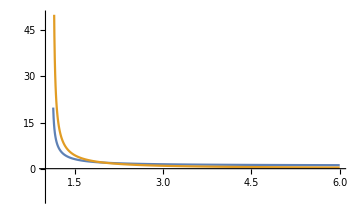

```mathematica
Plot[{(10.3125-9.53125 b+0.390625 √(696.96+b (-1426.56+718.24b)))/(-1.125+b),-10.4688+(9.43689*10^-15)/(1.125- b)^2-0.410156/(1.125- b)+(0.390625  √(696.96+b (-1426.56+718.24 b)))/(-1.125+ b)},{b,1,6},PlotRange->{{1,6},{-10,50}},ImageSize->Medium,MaxRecursion->4]
```

So the threshold value for alpha2 is 1.125 given η=1 (in order for the system to reach a steady state. But why????

```mathematica
(1+(τ*δ(1/α1A-1/α2A))/(1-2δ(1/α1A+1/α2A)))+((1-(τ*δ(1/α1A-1/α2A))/(1-2δ(1/α1A+1/α2A)))^2-2((τ*δ(1/α1A-1/α2A))/(1-2δ(1/α1A+1/α2A))))^(1/2)/.{k->10,δ->0.6,τ->0.2,α1A->2,α2A->6}
(1-(τ*δ(1/α1A-1/α2A))/(1-2δ(1/α1A+1/α2A)))+((1-(τ*δ(1/α1A-1/α2A))/(1-2δ(1/α1A+1/α2A)))^2-2((τ*δ(1/α1A-1/α2A))/(1-2δ(1/α1A+1/α2A))))^(1/2)/.{k->10,δ->0.6,τ->0.2,α1A->2,α2A->6}
```

1.6899

1.2899

```mathematica
(*η=3; δ1=0.6; δ2 = δ1 ; k = 10; τ=0.2; f = 0; n = 16;b =1;
α1A = 2; α2A = 2; α1B =b; α2B =b;
eqeq = FullSimplify[Solve[f1==0&&f2==0&&f3p==0 && f4p==0 && f5p==0&&f6p==0,{s1,s2,n1A,n2A,n1B,n2B}],$Assumptions];
{s1,s2,n1A,n2A,n1B,n2B, (n1A+n2A+n1B+n2B)/n ,(n1A+n2A+n1B+n2B)/n≤ 1}/.eqeq// MatrixForm

DeleteDuplicates[f1/.eqeq]
DeleteDuplicates[f2/.eqeq]*)
```

OK, let’s plot these and see if we can get something similar to Chris’s results!

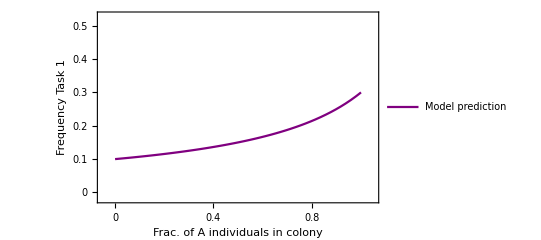

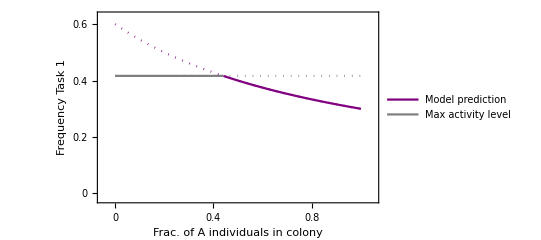

0.0625

```mathematica
a1 = 2;
τ=0.2;

a2 = 6;
Plot[Min[1/(2(1+τ)),0.6/(f*a1+(1-f)*a2)],{f,0,1},PlotRange->{{-0.05,1.05},{-0.02,0.53}},PlotLabel->"", (* (Subscript[α, 1]^B= 6) *)
Axes->False,Frame->{{True,False},{True,False}},LabelStyle->Black,PlotStyle->Purple, FrameLabel->{{"Frequency Task 1",None},{"Frac. of A individuals in colony",None}},FrameTicks->All, AspectRatio->0.6,PlotLegends->{Style["Model prediction",10]}]

a2 = 1;
Plot[{1.2/(f*a1+(1-f)*a2)*HeavisideTheta[f-0.44]-0.6/(f*a1+(1-f)*a2),1/(1+τ)*HeavisideTheta[0.44-f]-1/(2(1+τ)),0.6/(f*a1+(1-f)*a2),1/(2(1+τ))},{f,0,1},PlotRange->{{-0.05,1.05},{-0.02,0.63}},PlotLabel->"", (* (Subscript[α, 1]^B= 1) *)PlotStyle->{{Line,Purple},{Line,Gray},{Dotted,Purple},{Dotted,Gray}},
Axes->False,Frame->{{True,False},{True,False}},LabelStyle->Black,PlotLegends->Placed[{Style["Model prediction",10],Style["Max activity level",10]},After],FrameLabel->{{"Frequency Task 1",None},{"Frac. of A individuals in colony",None}},FrameTicks->All, AspectRatio->0.6]
0.25/4
```

```mathematica
NSolve[0.6/(f*a1+(1-f)*a2) == 1/(2(1+τ)),f]
```

{}

## Changing the stimulus equations (50-50 mixes only) Last updated: February 13, 2019 What happens when the stimulus equations are NOT normalized?? (See f1p and f2p below)

```mathematica
ClearAll["Global`*"]
```

```mathematica
P1A[s1_,μ1A_,η_]:=s1^η/(s1^η+μ1A^η)
P2A[s2_,μ2A_,η_]:=s2^η/(s2^η+μ2A^η)
P1B[s1_,μ1B_,η_]:=s1^η/(s1^η+μ1B^η)
P2B[s2_,μ2B_,η_]:=s2^η/(s2^η+μ2B^η)
```

```mathematica
(*f1:=δ1 -(α1A*n1A + α1B*n1B)/n
f2:=δ2 -(α2A*n2A + α2B*n2B)/n*)
f1p:=n*δ1 -(α1A*n1A + α1B*n1B)
f2p:=n*δ2 -(α2A*n2A + α2B*n2B)

(*f3:=1/2*P1A[s1,μ1A,η](n/2-(n1A+n2A)) - τ*n1A
f4:=1/2*P2A[s2,μ2A,η](n/2-(n1A+n2A)) - τ*n2A
f5:=1/2*P1B[s1,μ1B,η](n/2-(n1B+n2B)) - τ*n1B
f6:=1/2*P2B[s2,μ2B,η](n/2-(n1B+n2B)) - τ*n2B*)
f3p:=1/2*P1A[s1,μ1A,η]*(2-P2A[s2,μ2A,η])*(n/2-(n1A+n2A)) - τ*n1A
f4p:=1/2*P2A[s2,μ2A,η]*(2-P1A[s1,μ1A,η])*(n/2-(n1A+n2A)) - τ*n2A
f5p:=1/2*P1B[s1,μ1B,η]*(2-P2B[s2,μ2B,η])*(n/2-(n1B+n2B)) - τ*n1B
f6p:=1/2*P2B[s2,μ2B,η]*(2-P1B[s1,μ1B,η])*(n/2-(n1B+n2B)) - τ*n2B
```

```mathematica
τ=0.2;
(*μ1A=10;μ2A=10;μ1B=10;μ2B=10;*)
μ1A=k;μ2A=k;μ1B=k;μ2B=k;
$Assumptions={s1,s2,n1A,n2A,n1B,n2B,δ1,δ2,α1A,α1B,α2A,α2B,μ1A,μ2A,μ1B,μ2B}∈Reals&&{s1,s2,n1A,n2A,n1B,n2B,δ1,δ2,α1A,α1B,α2A,α2B,μ1A,μ2A,μ1B,μ2B}≥0;
```

```mathematica
Off[Solve::ratnz];
(η=#;
eq=FullSimplify[Solve[f1p==0&&f2p==0&&f3p==0 && f4p==0 && f5p==0&&f6p==0,{s1,s2,n1A,n2A,n1B,n2B}],$Assumptions];

Print[{"η = "<>ToString[#],Length@eq,DeleteDuplicates[{n1A,n2A,n1B,n2B}/.eq]}];&)/@ {1}(*{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}*)
```

$Aborted

```mathematica
Clear[δ1,δ2,α1A,α1B,α2A,α2B,n,μ1A,μ2A,μ1B,μ2B];
n=16.;(*μ1A=10.;μ2A=20.;μ1B=20.;μ2B=10.;*)
δ1=0.6; δ2=0.6;
(*Reduce[f1==0&&f2==0&&f3==0 && f4==0 && f5==0&&f6==0&&$Assumptions,{s1,s2,n1A,n2A,n1B,n2B}]*)
(*Solve[f1==0&&f2==0&&f3==0 && f4==0 && f5==0&&f6==0,{s1,s2,n1A,n2A,n1B,n2B}]*)
μ1A =10 ; μ2A = 2*μ1A; μ1B = 2*μ1A; μ2B =μ1A;
α1A=2;α1B=α1A;α2A=α1A;α2B=α1A;

eq3=FullSimplify[Solve[f1==0&&f2==0&&f3==0 && f4==0 && f5==0&&f6==0,{s1,s2,n1A,n2A,n1B,n2B}] ,$Assumptions];
eq4=DeleteDuplicates[FullSimplify[{n1A,n2A,n1B,n2B}/.eq3,$Assumptions]]
Length@eq4

f1
f2
f3
f4
f5
f6
```

{n1A,n2A,n1B,n2B}

4

f1

f2

f3

f4

f5

f6

Why can’t the equilibria be computed when μ1B = μ2B = 2*μ1A???

```mathematica
FullSimplify[{f1,f2,f3,f4,f5,f6}/.{n1A->(n δ1)/(α1A+α1B),n2A->(n δ2)/(α2A+α2B),n1B->(n δ1)/(α1A+α1B),n2B->(n δ2)/(α2A+α2B)} ] // MatrixForm
```

(f1
f2
f3
f4
f5
f6)

```mathematica
eq2
```

eq2

## Different μ’s under symmetric task performance (50-50 mixes only) Last updated: February 14, 2019 Assume identical α’s and δ’s, and “symmetric” μ values, i.e., μ_1^A=μ_2^B=a, μ_1^B=μ_2^A=b. What happens? Can we compute the equilibrium values explicitly?

```mathematica
ClearAll["Global`*"]
```

```mathematica
P1A[s1_,μ1A_,η_]:=s1^η/(s1^η+μ1A^η)
P2A[s2_,μ2A_,η_]:=s2^η/(s2^η+μ2A^η)
P1B[s1_,μ1B_,η_]:=s1^η/(s1^η+μ1B^η)
P2B[s2_,μ2B_,η_]:=s2^η/(s2^η+μ2B^η)
```

```mathematica
f1:=δ1 -(α1A*n1A + α1B*n1B)/n
f2:=δ2 -(α2A*n2A + α2B*n2B)/n

(*f3:=1/2*P1A[s1,μ1A,η](n/2-(n1A+n2A)) - τ*n1A
f4:=1/2*P2A[s2,μ2A,η](n/2-(n1A+n2A)) - τ*n2A
f5:=1/2*P1B[s1,μ1B,η](n/2-(n1B+n2B)) - τ*n1B
f6:=1/2*P2B[s2,μ2B,η](n/2-(n1B+n2B)) - τ*n2B*)
f3p:=1/2*P1A[s1,μ1A,η]*(2-P2A[s2,μ2A,η])*(n/2-(n1A+n2A)) - τ*n1A
f4p:=1/2*P2A[s2,μ2A,η]*(2-P1A[s1,μ1A,η])*(n/2-(n1A+n2A)) - τ*n2A
f5p:=1/2*P1B[s1,μ1B,η]*(2-P2B[s2,μ2B,η])*(n/2-(n1B+n2B)) - τ*n1B
f6p:=1/2*P2B[s2,μ2B,η]*(2-P1B[s1,μ1B,η])*(n/2-(n1B+n2B)) - τ*n2B
```

```mathematica
(*Clear[η]*)
η=1;
δ1=δ; δ2=δ;
μ1A=a;μ2A=b;μ1B=b;μ2B=a;
α1A=α;α1B=α;α2A=α;α2B=α;
$Assumptions={s1,s2,n1A,n2A,n1B,n2B,δ1,δ2,α1A,α1B,α2A,α2B,μ1A,μ2A,μ1B,μ2B,a,b,α}∈Reals&&{s1,s2,n1A,n2A,n1B,n2B,δ1,δ2,α1A,α1B,α2A,α2B,μ1A,μ2A,μ1B,μ2B,a,b,α}≥0;
```

```mathematica
η=1;
n1Asol = First@Solve[f1==0,n1A] // FullSimplify
n2Asol = First@Solve[f2==0,n2A] // FullSimplify
s1sol =First@Solve[f3p==0, s1] // FullSimplify
f4p/.s1sol/.n1Asol/.n2Asol// FullSimplify
f5p/.s1sol/.n1Asol/.n2Asol// FullSimplify
f6p/.s1sol/.n1Asol/.n2Asol// FullSimplify
```

{n1A→-n1B+(n δ)/α}

{n2A→-n2B+(n δ)/α}

{s1→-(4 a n1A (b+s2) τ)/(-(n-2 (n1A+n2A)) (2 b+s2)+4 n1A (b+s2) τ)}

((s2 (2 (n1B+n2B) α+n (α-4 δ)))/(b+s2)+(2 (2 b n2B α+(n1B+n2B) s2 α-2 n (b+s2) δ) τ)/(2 b+s2))/(2 α)

-n1B τ+(a (n-2 (n1B+n2B)) (2 a+s2) (b+s2) (-n1B α+n δ) τ)/((a+s2) (b (2 b+s2) (2 (n1B+n2B) α+n (α-4 δ))+4 (-a+b) (b+s2) (n1B α-n δ) τ))

-n2B τ+((n-2 (n1B+n2B)) s2 (b (2 b+s2) (2 (n1B+n2B) α+n (α-4 δ))-2 (a-2 b) (b+s2) (n1B α-n δ) τ))/(2 (a+s2) (b (2 b+s2) (2 (n1B+n2B) α+n (α-4 δ))+4 (-a+b) (b+s2) (n1B α-n δ) τ))

```mathematica
f4psub:=1/(2 α2A)(2 (n2B α2B-n δ2) τ+(s2 (n α1A α2A+2 n1B α1B α2A+2 n2B α1A α2B-2 n α2A δ1-2 n α1A δ2) ((n α1A α2A+2 n1B α1B α2A+2 n2B α1A α2B-2 n α2A δ1-2 n α1A δ2) (s2+2 μ1A) μ2A-2 α2A (n1B α1B-n δ1) (s2+μ1A) (μ1A-2 μ2A) τ))/(α1A (s2+μ2A) ((n α1A α2A+2 n1B α1B α2A+2 n2B α1A α2B-2 n α2A δ1-2 n α1A δ2) (s2+2 μ1A) μ2A-4 α2A (n1B α1B-n δ1) (s2+μ1A) (μ1A-μ2A) τ)))
```

```mathematica
f5psub:=-n1B τ+((n-2 (n1B+n2B)) α2A (-n1B α1B+n δ1) μ1A (s2+μ1A) (s2+2 μ1B) τ)/((s2+μ1B) ((n α1A α2A+2 n1B α1B α2A+2 n2B α1A α2B-2 n α2A δ1-2 n α1A δ2) (s2+2 μ1A) μ1B-4 α2A (n1B α1B-n δ1) (s2+μ1A) (μ1A-μ1B) τ))
```

```mathematica
f6psub:=-n2B τ+((n-2 (n1B+n2B)) s2 ((n α1A α2A+2 n1B α1B α2A+2 n2B α1A α2B-2 n α2A δ1-2 n α1A δ2) (s2+2 μ1A) μ2B-2 α2A (n1B α1B-n δ1) (s2+μ1A) (μ1A-2 μ2B) τ))/(2 (s2+μ2B) ((n α1A α2A+2 n1B α1B α2A+2 n2B α1A α2B-2 n α2A δ1-2 n α1A δ2) (s2+2 μ1A) μ2B-4 α2A (n1B α1B-n δ1) (s2+μ1A) (μ1A-μ2B) τ))
```

```mathematica
Solve[f4psub==0&&f5psub==0&&f6psub==0,{s2,n1B,n2B}]
```

$Aborted

```mathematica
(η=#;
(*eq2 = FullSimplify[Solve[f1==0&&f3p==0 && f4p==0,{s1,n1A,n2A}],$Assumptions];*)
eq2 = Solve[(f1/.{n1A->k, n2B->k,n2A->m, n1B->m})==0&&(f3p/.{s1->s,s2->s,n1A->k, n2B->k,n2A->m, n1B->m})==0 && (f4p/.{s1->s,s2->s,n1A->k, n2B->k,n2A->m, n1B->m})==0,{s,k,m}];
(*eq2 = eq2/.{a->10, b->20, α->2,δ->0.6,n->16};*)
Print[{"η = "<>ToString[#],Length@eq2,MatrixForm@Chop@DeleteDuplicates[{s,k/8,m/8}/.eq2]}];&)/@{1}(* {1,2,3,4,5,6,7}*)
```

{η = 1,4,(1/2 (-a-b)-1/2 √((a+b)^2-(a^2 α+8 a b α+b^2 α-2 a^2 δ-16 a b δ-2 b^2 δ-4 a^2 δ τ-16 a b δ τ-4 b^2 δ τ)/(2 (α-2 δ-2 δ τ))-(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)/(6 (α-2 δ-2 δ τ))-((-a^2 α+4 a b α-b^2 α+2 a^2 δ-8 a b δ+2 b^2 δ+4 a^2 δ τ-8 a b δ τ+4 b^2 δ τ)^2)/(3 2^(2/3) (α-2 δ-2 δ τ) (1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2+√(-4 (-96 a^2 b^2 δ τ (α-2 δ-2 δ τ)+(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^2-24 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ))^3+(1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2)^2))^(1/3))-((1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2+√(-4 (-96 a^2 b^2 δ τ (α-2 δ-2 δ τ)+(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^2-24 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ))^3+(1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2)^2))^(1/3))/(6 2^(1/3) (α-2 δ-2 δ τ)))-1/2 √(2 (a+b)^2-(a^2 α+8 a b α+b^2 α-2 a^2 δ-16 a b δ-2 b^2 δ-4 a^2 δ τ-16 a b δ τ-4 b^2 δ τ)/(2 (α-2 δ-2 δ τ))+(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)/(6 (α-2 δ-2 δ τ))+((-a^2 α+4 a b α-b^2 α+2 a^2 δ-8 a b δ+2 b^2 δ+4 a^2 δ τ-8 a b δ τ+4 b^2 δ τ)^2)/(3 2^(2/3) (α-2 δ-2 δ τ) (1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2+√(-4 (-96 a^2 b^2 δ τ (α-2 δ-2 δ τ)+(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^2-24 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ))^3+(1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2)^2))^(1/3))+((1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2+√(-4 (-96 a^2 b^2 δ τ (α-2 δ-2 δ τ)+(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^2-24 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ))^3+(1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2)^2))^(1/3))/(6 2^(1/3) (α-2 δ-2 δ τ))-(-8 (a+b)^3+(4 (a+b) (a^2 α+8 a b α+b^2 α-2 a^2 δ-16 a b δ-2 b^2 δ-4 a^2 δ τ-16 a b δ τ-4 b^2 δ τ))/(α-2 δ-2 δ τ)-(8 (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ))/(α-2 δ-2 δ τ))/(4 √((a+b)^2-(a^2 α+8 a b α+b^2 α-2 a^2 δ-16 a b δ-2 b^2 δ-4 a^2 δ τ-16 a b δ τ-4 b^2 δ τ)/(2 (α-2 δ-2 δ τ))-(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)/(6 (α-2 δ-2 δ τ))-((-a^2 α+4 a b α-b^2 α+2 a^2 δ-8 a b δ+2 b^2 δ+4 a^2 δ τ-8 a b δ τ+4 b^2 δ τ)^2)/(3 2^(2/3) (α-2 δ-2 δ τ) (1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2+√(-4 (-96 a^2 b^2 δ τ (α-2 δ-2 δ τ)+(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^2-24 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ))^3+(1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2)^2))^(1/3))-((1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2+√(-4 (-96 a^2 b^2 δ τ (α-2 δ-2 δ τ)+(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^2-24 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ))^3+(1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2)^2))^(1/3))/(6 2^(1/3) (α-2 δ-2 δ τ))))) | (6 a b^2 n δ τ-2 b^3 n δ τ+a^2 n α (1/2 (-a-b)-1/2 √((a+b)^2-(a^2 α+8 a b α+b^2 α-2 a^2 δ-16 a b δ-2 b^2 δ-4 a^2 δ τ-16 a b δ τ-4 b^2 δ τ)/(2 (α-2 δ-2 δ τ))-(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)/(6 (α-2 δ-2 δ τ))-((-a^2 α+4 a b α-b^2 α+2 a^2 δ-8 a b δ+2 b^2 δ+4 a^2 δ τ-8 a b δ τ+4 b^2 δ τ)^2)/(3 2^(2/3) (α-2 δ-2 δ τ) (1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2+√(-4 (-96 a^2 b^2 δ τ (α-2 δ-2 δ τ)+(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^2-24 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ))^3+(1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2)^2))^(1/3))-((1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2+√(-4 (-96 a^2 b^2 δ τ (α-2 δ-2 δ τ)+(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^2-24 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ))^3+(1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2)^2))^(1/3))/(6 2^(1/3) (α-2 δ-2 δ τ)))-1/2 √(2 (a+b)^2-(a^2 α+8 a b α+b^2 α-2 a^2 δ-16 a b δ-2 b^2 δ-4 a^2 δ τ-16 a b δ τ-4 b^2 δ τ)/(2 (α-2 δ-2 δ τ))+(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)/(6 (α-2 δ-2 δ τ))+((-a^2 α+4 a b α-b^2 α+2 a^2 δ-8 a b δ+2 b^2 δ+4 a^2 δ τ-8 a b δ τ+4 b^2 δ τ)^2)/(3 2^(2/3) (α-2 δ-2 δ τ) (1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2+√(-4 (-96 a^2 b^2 δ τ (α-2 δ-2 δ τ)+(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^2-24 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ))^3+(1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2)^2))^(1/3))+((1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2+√(-4 (-96 a^2 b^2 δ τ (α-2 δ-2 δ τ)+(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^2-24 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ))^3+(1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2)^2))^(1/3))/(6 2^(1/3) (α-2 δ-2 δ τ))-(-8 (a+b)^3+(4 (a+b) (a^2 α+8 a b α+b^2 α-2 a^2 δ-16 a b δ-2 b^2 δ-4 a^2 δ τ-16 a b δ τ-4 b^2 δ τ))/(α-2 δ-2 δ τ)-(8 (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ))/(α-2 δ-2 δ τ))/(4 √((a+b)^2-(a^2 α+8 a b α+b^2 α-2 a^2 δ-16 a b δ-2 b^2 δ-4 a^2 δ τ-16 a b δ τ-4 b^2 δ τ)/(2 (α-2 δ-2 δ τ))-(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)/(6 (α-2 δ-2 δ τ))-((-a^2 α+4 a b α-b^2 α+2 a^2 δ-8 a b δ+2 b^2 δ+4 a^2 δ τ-8 a b δ τ+4 b^2 δ τ)^2)/(3 2^(2/3) (α-2 δ-2 δ τ) (1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2+√(-4 (-96 a^2 b^2 δ τ (α-2 δ-2 δ τ)+(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^2-24 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ))^3+(1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2)^2))^(1/3))-((1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2+√(-4 (-96 a^2 b^2 δ τ (α-2 δ-2 δ τ)+(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^2-24 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ))^3+(1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2)^2))^(1/3))/(6 2^(1/3) (α-2 δ-2 δ τ))))))-6 a b n α (1/2 (-a-b)-1/2 √((a+b)^2-(a^2 α+8 a b α+b^2 α-2 a^2 δ-16 a b δ-2 b^2 δ-4 a^2 δ τ-16 a b δ τ-4 b^2 δ τ)/(2 (α-2 δ-2 δ τ))-(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)/(6 (α-2 δ-2 δ τ))-((-a^2 α+4 a b α-b^2 α+2 a^2 δ-8 a b δ+2 b^2 δ+4 a^2 δ τ-8 a b δ τ+4 b^2 δ τ)^2)/(3 2^(2/3) (α-2 δ-2 δ τ) (1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2+√(-4 (-96 a^2 b^2 δ τ (α-2 δ-2 δ τ)+(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^2-24 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ))^3+(1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2)^2))^(1/3))-((1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2+√(-4 (-96 a^2 b^2 δ τ (α-2 δ-2 δ τ)+(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^2-24 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ))^3+(1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2)^2))^(1/3))/(6 2^(1/3) (α-2 δ-2 δ τ)))-1/2 √(2 (a+b)^2-(a^2 α+8 a b α+b^2 α-2 a^2 δ-16 a b δ-2 b^2 δ-4 a^2 δ τ-16 a b δ τ-4 b^2 δ τ)/(2 (α-2 δ-2 δ τ))+(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)/(6 (α-2 δ-2 δ τ))+((-a^2 α+4 a b α-b^2 α+2 a^2 δ-8 a b δ+2 b^2 δ+4 a^2 δ τ-8 a b δ τ+4 b^2 δ τ)^2)/(3 2^(2/3) (α-2 δ-2 δ τ) (1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2+√(-4 (-96 a^2 b^2 δ τ (α-2 δ-2 δ τ)+(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^2-24 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ))^3+(1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2)^2))^(1/3))+((1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2+√(-4 (-96 a^2 b^2 δ τ (α-2 δ-2 δ τ)+(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^2-24 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ))^3+(1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2)^2))^(1/3))/(6 2^(1/3) (α-2 δ-2 δ τ))-(-8 (a+b)^3+(4 (a+b) (a^2 α+8 a b α+b^2 α-2 a^2 δ-16 a b δ-2 b^2 δ-4 a^2 δ τ-16 a b δ τ-4 b^2 δ τ))/(α-2 δ-2 δ τ)-(8 (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ))/(α-2 δ-2 δ τ))/(4 √((a+b)^2-(a^2 α+8 a b α+b^2 α-2 a^2 δ-16 a b δ-2 b^2 δ-4 a^2 δ τ-16 a b δ τ-4 b^2 δ τ)/(2 (α-2 δ-2 δ τ))-(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)/(6 (α-2 δ-2 δ τ))-((-a^2 α+4 a b α-b^2 α+2 a^2 δ-8 a b δ+2 b^2 δ+4 a^2 δ τ-8 a b δ τ+4 b^2 δ τ)^2)/(3 2^(2/3) (α-2 δ-2 δ τ) (1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2+√(-4 (-96 a^2 b^2 δ τ (α-2 δ-2 δ τ)+(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^2-24 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ))^3+(1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2)^2))^(1/3))-((1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2+√(-4 (-96 a^2 b^2 δ τ (α-2 δ-2 δ τ)+(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^2-24 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ))^3+(1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2)^2))^(1/3))/(6 2^(1/3) (α-2 δ-2 δ τ))))))+b^2 n α (1/2 (-a-b)-1/2 √((a+b)^2-(a^2 α+8 a b α+b^2 α-2 a^2 δ-16 a b δ-2 b^2 δ-4 a^2 δ τ-16 a b δ τ-4 b^2 δ τ)/(2 (α-2 δ-2 δ τ))-(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)/(6 (α-2 δ-2 δ τ))-((-a^2 α+4 a b α-b^2 α+2 a^2 δ-8 a b δ+2 b^2 δ+4 a^2 δ τ-8 a b δ τ+4 b^2 δ τ)^2)/(3 2^(2/3) (α-2 δ-2 δ τ) (1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2+√(-4 (-96 a^2 b^2 δ τ (α-2 δ-2 δ τ)+(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^2-24 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ))^3+(1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2)^2))^(1/3))-((1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2+√(-4 (-96 a^2 b^2 δ τ (α-2 δ-2 δ τ)+(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^2-24 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ))^3+(1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2)^2))^(1/3))/(6 2^(1/3) (α-2 δ-2 δ τ)))-1/2 √(2 (a+b)^2-(a^2 α+8 a b α+b^2 α-2 a^2 δ-16 a b δ-2 b^2 δ-4 a^2 δ τ-16 a b δ τ-4 b^2 δ τ)/(2 (α-2 δ-2 δ τ))+(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)/(6 (α-2 δ-2 δ τ))+((-a^2 α+4 a b α-b^2 α+2 a^2 δ-8 a b δ+2 b^2 δ+4 a^2 δ τ-8 a b δ τ+4 b^2 δ τ)^2)/(3 2^(2/3) (α-2 δ-2 δ τ) (1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2+√(-4 (-96 a^2 b^2 δ τ (α-2 δ-2 δ τ)+(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^2-24 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ))^3+(1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2)^2))^(1/3))+((1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2+√(-4 (-96 a^2 b^2 δ τ (α-2 δ-2 δ τ)+(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^2-24 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ))^3+(1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2)^2))^(1/3))/(6 2^(1/3) (α-2 δ-2 δ τ))-(-8 (a+b)^3+(4 (a+b) (a^2 α+8 a b α+b^2 α-2 a^2 δ-16 a b δ-2 b^2 δ-4 a^2 δ τ-16 a b δ τ-4 b^2 δ τ))/(α-2 δ-2 δ τ)-(8 (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ))/(α-2 δ-2 δ τ))/(4 √((a+b)^2-(a^2 α+8 a b α+b^2 α-2 a^2 δ-16 a b δ-2 b^2 δ-4 a^2 δ τ-16 a b δ τ-4 b^2 δ τ)/(2 (α-2 δ-2 δ τ))-(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)/(6 (α-2 δ-2 δ τ))-((-a^2 α+4 a b α-b^2 α+2 a^2 δ-8 a b δ+2 b^2 δ+4 a^2 δ τ-8 a b δ τ+4 b^2 δ τ)^2)/(3 2^(2/3) (α-2 δ-2 δ τ) (1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2+√(-4 (-96 a^2 b^2 δ τ (α-2 δ-2 δ τ)+(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^2-24 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ))^3+(1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2)^2))^(1/3))-((1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2+√(-4 (-96 a^2 b^2 δ τ (α-2 δ-2 δ τ)+(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^2-24 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ))^3+(1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2)^2))^(1/3))/(6 2^(1/3) (α-2 δ-2 δ τ))))))-2 a^2 n δ (1/2 (-a-b)-1/2 √((a+b)^2-(a^2 α+8 a b α+b^2 α-2 a^2 δ-16 a b δ-2 b^2 δ-4 a^2 δ τ-16 a b δ τ-4 b^2 δ τ)/(2 (α-2 δ-2 δ τ))-(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)/(6 (α-2 δ-2 δ τ))-((-a^2 α+4 a b α-b^2 α+2 a^2 δ-8 a b δ+2 b^2 δ+4 a^2 δ τ-8 a b δ τ+4 b^2 δ τ)^2)/(3 2^(2/3) (α-2 δ-2 δ τ) (1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2+√(-4 (-96 a^2 b^2 δ τ (α-2 δ-2 δ τ)+(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^2-24 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ))^3+(1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2)^2))^(1/3))-((1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2+√(-4 (-96 a^2 b^2 δ τ (α-2 δ-2 δ τ)+(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^2-24 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ))^3+(1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2)^2))^(1/3))/(6 2^(1/3) (α-2 δ-2 δ τ)))-1/2 √(2 (a+b)^2-(a^2 α+8 a b α+b^2 α-2 a^2 δ-16 a b δ-2 b^2 δ-4 a^2 δ τ-16 a b δ τ-4 b^2 δ τ)/(2 (α-2 δ-2 δ τ))+(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)/(6 (α-2 δ-2 δ τ))+((-a^2 α+4 a b α-b^2 α+2 a^2 δ-8 a b δ+2 b^2 δ+4 a^2 δ τ-8 a b δ τ+4 b^2 δ τ)^2)/(3 2^(2/3) (α-2 δ-2 δ τ) (1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2+√(-4 (-96 a^2 b^2 δ τ (α-2 δ-2 δ τ)+(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^2-24 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ))^3+(1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2)^2))^(1/3))+((1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2+√(-4 (-96 a^2 b^2 δ τ (α-2 δ-2 δ τ)+(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^2-24 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ))^3+(1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2)^2))^(1/3))/(6 2^(1/3) (α-2 δ-2 δ τ))-(-8 (a+b)^3+(4 (a+b) (a^2 α+8 a b α+b^2 α-2 a^2 δ-16 a b δ-2 b^2 δ-4 a^2 δ τ-16 a b δ τ-4 b^2 δ τ))/(α-2 δ-2 δ τ)-(8 (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ))/(α-2 δ-2 δ τ))/(4 √((a+b)^2-(a^2 α+8 a b α+b^2 α-2 a^2 δ-16 a b δ-2 b^2 δ-4 a^2 δ τ-16 a b δ τ-4 b^2 δ τ)/(2 (α-2 δ-2 δ τ))-(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)/(6 (α-2 δ-2 δ τ))-((-a^2 α+4 a b α-b^2 α+2 a^2 δ-8 a b δ+2 b^2 δ+4 a^2 δ τ-8 a b δ τ+4 b^2 δ τ)^2)/(3 2^(2/3) (α-2 δ-2 δ τ) (1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2+√(-4 (-96 a^2 b^2 δ τ (α-2 δ-2 δ τ)+(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^2-24 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ))^3+(1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2)^2))^(1/3))-((1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2+√(-4 (-96 a^2 b^2 δ τ (α-2 δ-2 δ τ)+(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^2-24 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ))^3+(1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2)^2))^(1/3))/(6 2^(1/3) (α-2 δ-2 δ τ))))))+12 a b n δ (1/2 (-a-b)-1/2 √((a+b)^2-(a^2 α+8 a b α+b^2 α-2 a^2 δ-16 a b δ-2 b^2 δ-4 a^2 δ τ-16 a b δ τ-4 b^2 δ τ)/(2 (α-2 δ-2 δ τ))-(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)/(6 (α-2 δ-2 δ τ))-((-a^2 α+4 a b α-b^2 α+2 a^2 δ-8 a b δ+2 b^2 δ+4 a^2 δ τ-8 a b δ τ+4 b^2 δ τ)^2)/(3 2^(2/3) (α-2 δ-2 δ τ) (1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2+√(-4 (-96 a^2 b^2 δ τ (α-2 δ-2 δ τ)+(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^2-24 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ))^3+(1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2)^2))^(1/3))-((1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2+√(-4 (-96 a^2 b^2 δ τ (α-2 δ-2 δ τ)+(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^2-24 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ))^3+(1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2)^2))^(1/3))/(6 2^(1/3) (α-2 δ-2 δ τ)))-1/2 √(2 (a+b)^2-(a^2 α+8 a b α+b^2 α-2 a^2 δ-16 a b δ-2 b^2 δ-4 a^2 δ τ-16 a b δ τ-4 b^2 δ τ)/(2 (α-2 δ-2 δ τ))+(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)/(6 (α-2 δ-2 δ τ))+((-a^2 α+4 a b α-b^2 α+2 a^2 δ-8 a b δ+2 b^2 δ+4 a^2 δ τ-8 a b δ τ+4 b^2 δ τ)^2)/(3 2^(2/3) (α-2 δ-2 δ τ) (1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2+√(-4 (-96 a^2 b^2 δ τ (α-2 δ-2 δ τ)+(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^2-24 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ))^3+(1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2)^2))^(1/3))+((1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2+√(-4 (-96 a^2 b^2 δ τ (α-2 δ-2 δ τ)+(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^2-24 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ))^3+(1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2)^2))^(1/3))/(6 2^(1/3) (α-2 δ-2 δ τ))-(-8 (a+b)^3+(4 (a+b) (a^2 α+8 a b α+b^2 α-2 a^2 δ-16 a b δ-2 b^2 δ-4 a^2 δ τ-16 a b δ τ-4 b^2 δ τ))/(α-2 δ-2 δ τ)-(8 (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ))/(α-2 δ-2 δ τ))/(4 √((a+b)^2-(a^2 α+8 a b α+b^2 α-2 a^2 δ-16 a b δ-2 b^2 δ-4 a^2 δ τ-16 a b δ τ-4 b^2 δ τ)/(2 (α-2 δ-2 δ τ))-(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)/(6 (α-2 δ-2 δ τ))-((-a^2 α+4 a b α-b^2 α+2 a^2 δ-8 a b δ+2 b^2 δ+4 a^2 δ τ-8 a b δ τ+4 b^2 δ τ)^2)/(3 2^(2/3) (α-2 δ-2 δ τ) (1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2+√(-4 (-96 a^2 b^2 δ τ (α-2 δ-2 δ τ)+(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^2-24 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ))^3+(1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2)^2))^(1/3))-((1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2+√(-4 (-96 a^2 b^2 δ τ (α-2 δ-2 δ τ)+(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^2-24 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ))^3+(1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2)^2))^(1/3))/(6 2^(1/3) (α-2 δ-2 δ τ))))))-2 b^2 n δ (1/2 (-a-b)-1/2 √((a+b)^2-(a^2 α+8 a b α+b^2 α-2 a^2 δ-16 a b δ-2 b^2 δ-4 a^2 δ τ-16 a b δ τ-4 b^2 δ τ)/(2 (α-2 δ-2 δ τ))-(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)/(6 (α-2 δ-2 δ τ))-((-a^2 α+4 a b α-b^2 α+2 a^2 δ-8 a b δ+2 b^2 δ+4 a^2 δ τ-8 a b δ τ+4 b^2 δ τ)^2)/(3 2^(2/3) (α-2 δ-2 δ τ) (1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2+√(-4 (-96 a^2 b^2 δ τ (α-2 δ-2 δ τ)+(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^2-24 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ))^3+(1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2)^2))^(1/3))-((1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2+√(-4 (-96 a^2 b^2 δ τ (α-2 δ-2 δ τ)+(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^2-24 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ))^3+(1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2)^2))^(1/3))/(6 2^(1/3) (α-2 δ-2 δ τ)))-1/2 √(2 (a+b)^2-(a^2 α+8 a b α+b^2 α-2 a^2 δ-16 a b δ-2 b^2 δ-4 a^2 δ τ-16 a b δ τ-4 b^2 δ τ)/(2 (α-2 δ-2 δ τ))+(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)/(6 (α-2 δ-2 δ τ))+((-a^2 α+4 a b α-b^2 α+2 a^2 δ-8 a b δ+2 b^2 δ+4 a^2 δ τ-8 a b δ τ+4 b^2 δ τ)^2)/(3 2^(2/3) (α-2 δ-2 δ τ) (1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2+√(-4 (-96 a^2 b^2 δ τ (α-2 δ-2 δ τ)+(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^2-24 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ))^3+(1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2)^2))^(1/3))+((1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2+√(-4 (-96 a^2 b^2 δ τ (α-2 δ-2 δ τ)+(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^2-24 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ))^3+(1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2)^2))^(1/3))/(6 2^(1/3) (α-2 δ-2 δ τ))-(-8 (a+b)^3+(4 (a+b) (a^2 α+8 a b α+b^2 α-2 a^2 δ-16 a b δ-2 b^2 δ-4 a^2 δ τ-16 a b δ τ-4 b^2 δ τ))/(α-2 δ-2 δ τ)-(8 (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ))/(α-2 δ-2 δ τ))/(4 √((a+b)^2-(a^2 α+8 a b α+b^2 α-2 a^2 δ-16 a b δ-2 b^2 δ-4 a^2 δ τ-16 a b δ τ-4 b^2 δ τ)/(2 (α-2 δ-2 δ τ))-(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)/(6 (α-2 δ-2 δ τ))-((-a^2 α+4 a b α-b^2 α+2 a^2 δ-8 a b δ+2 b^2 δ+4 a^2 δ τ-8 a b δ τ+4 b^2 δ τ)^2)/(3 2^(2/3) (α-2 δ-2 δ τ) (1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2+√(-4 (-96 a^2 b^2 δ τ (α-2 δ-2 δ τ)+(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^2-24 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ))^3+(1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2)^2))^(1/3))-((1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2+√(-4 (-96 a^2 b^2 δ τ (α-2 δ-2 δ τ)+(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^2-24 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ))^3+(1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2)^2))^(1/3))/(6 2^(1/3) (α-2 δ-2 δ τ))))))+12 a b n δ τ (1/2 (-a-b)-1/2 √((a+b)^2-(a^2 α+8 a b α+b^2 α-2 a^2 δ-16 a b δ-2 b^2 δ-4 a^2 δ τ-16 a b δ τ-4 b^2 δ τ)/(2 (α-2 δ-2 δ τ))-(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)/(6 (α-2 δ-2 δ τ))-((-a^2 α+4 a b α-b^2 α+2 a^2 δ-8 a b δ+2 b^2 δ+4 a^2 δ τ-8 a b δ τ+4 b^2 δ τ)^2)/(3 2^(2/3) (α-2 δ-2 δ τ) (1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2+√(-4 (-96 a^2 b^2 δ τ (α-2 δ-2 δ τ)+(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^2-24 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ))^3+(1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2)^2))^(1/3))-((1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2+√(-4 (-96 a^2 b^2 δ τ (α-2 δ-2 δ τ)+(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^2-24 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ))^3+(1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2)^2))^(1/3))/(6 2^(1/3) (α-2 δ-2 δ τ)))-1/2 √(2 (a+b)^2-(a^2 α+8 a b α+b^2 α-2 a^2 δ-16 a b δ-2 b^2 δ-4 a^2 δ τ-16 a b δ τ-4 b^2 δ τ)/(2 (α-2 δ-2 δ τ))+(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)/(6 (α-2 δ-2 δ τ))+((-a^2 α+4 a b α-b^2 α+2 a^2 δ-8 a b δ+2 b^2 δ+4 a^2 δ τ-8 a b δ τ+4 b^2 δ τ)^2)/(3 2^(2/3) (α-2 δ-2 δ τ) (1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2+√(-4 (-96 a^2 b^2 δ τ (α-2 δ-2 δ τ)+(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^2-24 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ))^3+(1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2)^2))^(1/3))+((1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2+√(-4 (-96 a^2 b^2 δ τ (α-2 δ-2 δ τ)+(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^2-24 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ))^3+(1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2)^2))^(1/3))/(6 2^(1/3) (α-2 δ-2 δ τ))-(-8 (a+b)^3+(4 (a+b) (a^2 α+8 a b α+b^2 α-2 a^2 δ-16 a b δ-2 b^2 δ-4 a^2 δ τ-16 a b δ τ-4 b^2 δ τ))/(α-2 δ-2 δ τ)-(8 (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ))/(α-2 δ-2 δ τ))/(4 √((a+b)^2-(a^2 α+8 a b α+b^2 α-2 a^2 δ-16 a b δ-2 b^2 δ-4 a^2 δ τ-16 a b δ τ-4 b^2 δ τ)/(2 (α-2 δ-2 δ τ))-(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)/(6 (α-2 δ-2 δ τ))-((-a^2 α+4 a b α-b^2 α+2 a^2 δ-8 a b δ+2 b^2 δ+4 a^2 δ τ-8 a b δ τ+4 b^2 δ τ)^2)/(3 2^(2/3) (α-2 δ-2 δ τ) (1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2+√(-4 (-96 a^2 b^2 δ τ (α-2 δ-2 δ τ)+(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^2-24 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ))^3+(1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2)^2))^(1/3))-((1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2+√(-4 (-96 a^2 b^2 δ τ (α-2 δ-2 δ τ)+(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^2-24 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ))^3+(1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2)^2))^(1/3))/(6 2^(1/3) (α-2 δ-2 δ τ))))))-3 a n α ((1/2 (-a-b)-1/2 √((a+b)^2-(a^2 α+8 a b α+b^2 α-2 a^2 δ-16 a b δ-2 b^2 δ-4 a^2 δ τ-16 a b δ τ-4 b^2 δ τ)/(2 (α-2 δ-2 δ τ))-(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)/(6 (α-2 δ-2 δ τ))-((-a^2 α+4 a b α-b^2 α+2 a^2 δ-8 a b δ+2 b^2 δ+4 a^2 δ τ-8 a b δ τ+4 b^2 δ τ)^2)/(3 2^(2/3) (α-2 δ-2 δ τ) (1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2+√(-4 (-96 a^2 b^2 δ τ (α-2 δ-2 δ τ)+(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^2-24 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ))^3+(1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2)^2))^(1/3))-((1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2+√(-4 (-96 a^2 b^2 δ τ (α-2 δ-2 δ τ)+(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^2-24 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ))^3+(1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2)^2))^(1/3))/(6 2^(1/3) (α-2 δ-2 δ τ)))-1/2 √(2 (a+b)^2-(a^2 α+8 a b α+b^2 α-2 a^2 δ-16 a b δ-2 b^2 δ-4 a^2 δ τ-16 a b δ τ-4 b^2 δ τ)/(2 (α-2 δ-2 δ τ))+(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)/(6 (α-2 δ-2 δ τ))+((-a^2 α+4 a b α-b^2 α+2 a^2 δ-8 a b δ+2 b^2 δ+4 a^2 δ τ-8 a b δ τ+4 b^2 δ τ)^2)/(3 2^(2/3) (α-2 δ-2 δ τ) (1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2+√(-4 (-96 a^2 b^2 δ τ (α-2 δ-2 δ τ)+(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^2-24 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ))^3+(1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2)^2))^(1/3))+((1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2+√(-4 (-96 a^2 b^2 δ τ (α-2 δ-2 δ τ)+(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^2-24 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ))^3+(1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2)^2))^(1/3))/(6 2^(1/3) (α-2 δ-2 δ τ))-(-8 (a+b)^3+(4 (a+b) (a^2 α+8 a b α+b^2 α-2 a^2 δ-16 a b δ-2 b^2 δ-4 a^2 δ τ-16 a b δ τ-4 b^2 δ τ))/(α-2 δ-2 δ τ)-(8 (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ))/(α-2 δ-2 δ τ))/(4 √((a+b)^2-(a^2 α+8 a b α+b^2 α-2 a^2 δ-16 a b δ-2 b^2 δ-4 a^2 δ τ-16 a b δ τ-4 b^2 δ τ)/(2 (α-2 δ-2 δ τ))-(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)/(6 (α-2 δ-2 δ τ))-((-a^2 α+4 a b α-b^2 α+2 a^2 δ-8 a b δ+2 b^2 δ+4 a^2 δ τ-8 a b δ τ+4 b^2 δ τ)^2)/(3 2^(2/3) (α-2 δ-2 δ τ) (1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2+√(-4 (-96 a^2 b^2 δ τ (α-2 δ-2 δ τ)+(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^2-24 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ))^3+(1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2)^2))^(1/3))-((1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2+√(-4 (-96 a^2 b^2 δ τ (α-2 δ-2 δ τ)+(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^2-24 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ))^3+(1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2)^2))^(1/3))/(6 2^(1/3) (α-2 δ-2 δ τ)))))))^2-3 b n α ((1/2 (-a-b)-1/2 √((a+b)^2-(a^2 α+8 a b α+b^2 α-2 a^2 δ-16 a b δ-2 b^2 δ-4 a^2 δ τ-16 a b δ τ-4 b^2 δ τ)/(2 (α-2 δ-2 δ τ))-(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)/(6 (α-2 δ-2 δ τ))-((-a^2 α+4 a b α-b^2 α+2 a^2 δ-8 a b δ+2 b^2 δ+4 a^2 δ τ-8 a b δ τ+4 b^2 δ τ)^2)/(3 2^(2/3) (α-2 δ-2 δ τ) (1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2+√(-4 (-96 a^2 b^2 δ τ (α-2 δ-2 δ τ)+(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^2-24 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ))^3+(1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2)^2))^(1/3))-((1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2+√(-4 (-96 a^2 b^2 δ τ (α-2 δ-2 δ τ)+(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^2-24 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ))^3+(1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2)^2))^(1/3))/(6 2^(1/3) (α-2 δ-2 δ τ)))-1/2 √(2 (a+b)^2-(a^2 α+8 a b α+b^2 α-2 a^2 δ-16 a b δ-2 b^2 δ-4 a^2 δ τ-16 a b δ τ-4 b^2 δ τ)/(2 (α-2 δ-2 δ τ))+(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)/(6 (α-2 δ-2 δ τ))+((-a^2 α+4 a b α-b^2 α+2 a^2 δ-8 a b δ+2 b^2 δ+4 a^2 δ τ-8 a b δ τ+4 b^2 δ τ)^2)/(3 2^(2/3) (α-2 δ-2 δ τ) (1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2+√(-4 (-96 a^2 b^2 δ τ (α-2 δ-2 δ τ)+(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^2-24 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ))^3+(1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2)^2))^(1/3))+((1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2+√(-4 (-96 a^2 b^2 δ τ (α-2 δ-2 δ τ)+(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^2-24 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ))^3+(1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2)^2))^(1/3))/(6 2^(1/3) (α-2 δ-2 δ τ))-(-8 (a+b)^3+(4 (a+b) (a^2 α+8 a b α+b^2 α-2 a^2 δ-16 a b δ-2 b^2 δ-4 a^2 δ τ-16 a b δ τ-4 b^2 δ τ))/(α-2 δ-2 δ τ)-(8 (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ))/(α-2 δ-2 δ τ))/(4 √((a+b)^2-(a^2 α+8 a b α+b^2 α-2 a^2 δ-16 a b δ-2 b^2 δ-4 a^2 δ τ-16 a b δ τ-4 b^2 δ τ)/(2 (α-2 δ-2 δ τ))-(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)/(6 (α-2 δ-2 δ τ))-((-a^2 α+4 a b α-b^2 α+2 a^2 δ-8 a b δ+2 b^2 δ+4 a^2 δ τ-8 a b δ τ+4 b^2 δ τ)^2)/(3 2^(2/3) (α-2 δ-2 δ τ) (1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2+√(-4 (-96 a^2 b^2 δ τ (α-2 δ-2 δ τ)+(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^2-24 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ))^3+(1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2)^2))^(1/3))-((1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2+√(-4 (-96 a^2 b^2 δ τ (α-2 δ-2 δ τ)+(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^2-24 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ))^3+(1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2)^2))^(1/3))/(6 2^(1/3) (α-2 δ-2 δ τ)))))))^2+6 a n δ ((1/2 (-a-b)-1/2 √((a+b)^2-(a^2 α+8 a b α+b^2 α-2 a^2 δ-16 a b δ-2 b^2 δ-4 a^2 δ τ-16 a b δ τ-4 b^2 δ τ)/(2 (α-2 δ-2 δ τ))-(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)/(6 (α-2 δ-2 δ τ))-((-a^2 α+4 a b α-b^2 α+2 a^2 δ-8 a b δ+2 b^2 δ+4 a^2 δ τ-8 a b δ τ+4 b^2 δ τ)^2)/(3 2^(2/3) (α-2 δ-2 δ τ) (1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2+√(-4 (-96 a^2 b^2 δ τ (α-2 δ-2 δ τ)+(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^2-24 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ))^3+(1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2)^2))^(1/3))-((1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2+√(-4 (-96 a^2 b^2 δ τ (α-2 δ-2 δ τ)+(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^2-24 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ))^3+(1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2)^2))^(1/3))/(6 2^(1/3) (α-2 δ-2 δ τ)))-1/2 √(2 (a+b)^2-(a^2 α+8 a b α+b^2 α-2 a^2 δ-16 a b δ-2 b^2 δ-4 a^2 δ τ-16 a b δ τ-4 b^2 δ τ)/(2 (α-2 δ-2 δ τ))+(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)/(6 (α-2 δ-2 δ τ))+((-a^2 α+4 a b α-b^2 α+2 a^2 δ-8 a b δ+2 b^2 δ+4 a^2 δ τ-8 a b δ τ+4 b^2 δ τ)^2)/(3 2^(2/3) (α-2 δ-2 δ τ) (1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2+√(-4 (-96 a^2 b^2 δ τ (α-2 δ-2 δ τ)+(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^2-24 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ))^3+(1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2)^2))^(1/3))+((1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2+√(-4 (-96 a^2 b^2 δ τ (α-2 δ-2 δ τ)+(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^2-24 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ))^3+(1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2)^2))^(1/3))/(6 2^(1/3) (α-2 δ-2 δ τ))-(-8 (a+b)^3+(4 (a+b) (a^2 α+8 a b α+b^2 α-2 a^2 δ-16 a b δ-2 b^2 δ-4 a^2 δ τ-16 a b δ τ-4 b^2 δ τ))/(α-2 δ-2 δ τ)-(8 (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ))/(α-2 δ-2 δ τ))/(4 √((a+b)^2-(a^2 α+8 a b α+b^2 α-2 a^2 δ-16 a b δ-2 b^2 δ-4 a^2 δ τ-16 a b δ τ-4 b^2 δ τ)/(2 (α-2 δ-2 δ τ))-(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)/(6 (α-2 δ-2 δ τ))-((-a^2 α+4 a b α-b^2 α+2 a^2 δ-8 a b δ+2 b^2 δ+4 a^2 δ τ-8 a b δ τ+4 b^2 δ τ)^2)/(3 2^(2/3) (α-2 δ-2 δ τ) (1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2+√(-4 (-96 a^2 b^2 δ τ (α-2 δ-2 δ τ)+(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^2-24 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ))^3+(1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2)^2))^(1/3))-((1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2+√(-4 (-96 a^2 b^2 δ τ (α-2 δ-2 δ τ)+(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^2-24 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ))^3+(1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2)^2))^(1/3))/(6 2^(1/3) (α-2 δ-2 δ τ)))))))^2+6 b n δ ((1/2 (-a-b)-1/2 √((a+b)^2-(a^2 α+8 a b α+b^2 α-2 a^2 δ-16 a b δ-2 b^2 δ-4 a^2 δ τ-16 a b δ τ-4 b^2 δ τ)/(2 (α-2 δ-2 δ τ))-(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)/(6 (α-2 δ-2 δ τ))-((-a^2 α+4 a b α-b^2 α+2 a^2 δ-8 a b δ+2 b^2 δ+4 a^2 δ τ-8 a b δ τ+4 b^2 δ τ)^2)/(3 2^(2/3) (α-2 δ-2 δ τ) (1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2+√(-4 (-96 a^2 b^2 δ τ (α-2 δ-2 δ τ)+(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^2-24 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ))^3+(1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2)^2))^(1/3))-((1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2+√(-4 (-96 a^2 b^2 δ τ (α-2 δ-2 δ τ)+(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^2-24 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ))^3+(1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2)^2))^(1/3))/(6 2^(1/3) (α-2 δ-2 δ τ)))-1/2 √(2 (a+b)^2-(a^2 α+8 a b α+b^2 α-2 a^2 δ-16 a b δ-2 b^2 δ-4 a^2 δ τ-16 a b δ τ-4 b^2 δ τ)/(2 (α-2 δ-2 δ τ))+(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)/(6 (α-2 δ-2 δ τ))+((-a^2 α+4 a b α-b^2 α+2 a^2 δ-8 a b δ+2 b^2 δ+4 a^2 δ τ-8 a b δ τ+4 b^2 δ τ)^2)/(3 2^(2/3) (α-2 δ-2 δ τ) (1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2+√(-4 (-96 a^2 b^2 δ τ (α-2 δ-2 δ τ)+(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^2-24 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ))^3+(1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2)^2))^(1/3))+((1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2+√(-4 (-96 a^2 b^2 δ τ (α-2 δ-2 δ τ)+(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^2-24 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ))^3+(1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2)^2))^(1/3))/(6 2^(1/3) (α-2 δ-2 δ τ))-(-8 (a+b)^3+(4 (a+b) (a^2 α+8 a b α+b^2 α-2 a^2 δ-16 a b δ-2 b^2 δ-4 a^2 δ τ-16 a b δ τ-4 b^2 δ τ))/(α-2 δ-2 δ τ)-(8 (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ))/(α-2 δ-2 δ τ))/(4 √((a+b)^2-(a^2 α+8 a b α+b^2 α-2 a^2 δ-16 a b δ-2 b^2 δ-4 a^2 δ τ-16 a b δ τ-4 b^2 δ τ)/(2 (α-2 δ-2 δ τ))-(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)/(6 (α-2 δ-2 δ τ))-((-a^2 α+4 a b α-b^2 α+2 a^2 δ-8 a b δ+2 b^2 δ+4 a^2 δ τ-8 a b δ τ+4 b^2 δ τ)^2)/(3 2^(2/3) (α-2 δ-2 δ τ) (1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2+√(-4 (-96 a^2 b^2 δ τ (α-2 δ-2 δ τ)+(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^2-24 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ))^3+(1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2)^2))^(1/3))-((1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2+√(-4 (-96 a^2 b^2 δ τ (α-2 δ-2 δ τ)+(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^2-24 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ))^3+(1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2)^2))^(1/3))/(6 2^(1/3) (α-2 δ-2 δ τ)))))))^2+6 a n δ τ ((1/2 (-a-b)-1/2 √((a+b)^2-(a^2 α+8 a b α+b^2 α-2 a^2 δ-16 a b δ-2 b^2 δ-4 a^2 δ τ-16 a b δ τ-4 b^2 δ τ)/(2 (α-2 δ-2 δ τ))-(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)/(6 (α-2 δ-2 δ τ))-((-a^2 α+4 a b α-b^2 α+2 a^2 δ-8 a b δ+2 b^2 δ+4 a^2 δ τ-8 a b δ τ+4 b^2 δ τ)^2)/(3 2^(2/3) (α-2 δ-2 δ τ) (1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2+√(-4 (-96 a^2 b^2 δ τ (α-2 δ-2 δ τ)+(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^2-24 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ))^3+(1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2)^2))^(1/3))-((1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2+√(-4 (-96 a^2 b^2 δ τ (α-2 δ-2 δ τ)+(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^2-24 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ))^3+(1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2)^2))^(1/3))/(6 2^(1/3) (α-2 δ-2 δ τ)))-1/2 √(2 (a+b)^2-(a^2 α+8 a b α+b^2 α-2 a^2 δ-16 a b δ-2 b^2 δ-4 a^2 δ τ-16 a b δ τ-4 b^2 δ τ)/(2 (α-2 δ-2 δ τ))+(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)/(6 (α-2 δ-2 δ τ))+((-a^2 α+4 a b α-b^2 α+2 a^2 δ-8 a b δ+2 b^2 δ+4 a^2 δ τ-8 a b δ τ+4 b^2 δ τ)^2)/(3 2^(2/3) (α-2 δ-2 δ τ) (1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2+√(-4 (-96 a^2 b^2 δ τ (α-2 δ-2 δ τ)+(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^2-24 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ))^3+(1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2)^2))^(1/3))+((1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2+√(-4 (-96 a^2 b^2 δ τ (α-2 δ-2 δ τ)+(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^2-24 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ))^3+(1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2)^2))^(1/3))/(6 2^(1/3) (α-2 δ-2 δ τ))-(-8 (a+b)^3+(4 (a+b) (a^2 α+8 a b α+b^2 α-2 a^2 δ-16 a b δ-2 b^2 δ-4 a^2 δ τ-16 a b δ τ-4 b^2 δ τ))/(α-2 δ-2 δ τ)-(8 (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ))/(α-2 δ-2 δ τ))/(4 √((a+b)^2-(a^2 α+8 a b α+b^2 α-2 a^2 δ-16 a b δ-2 b^2 δ-4 a^2 δ τ-16 a b δ τ-4 b^2 δ τ)/(2 (α-2 δ-2 δ τ))-(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)/(6 (α-2 δ-2 δ τ))-((-a^2 α+4 a b α-b^2 α+2 a^2 δ-8 a b δ+2 b^2 δ+4 a^2 δ τ-8 a b δ τ+4 b^2 δ τ)^2)/(3 2^(2/3) (α-2 δ-2 δ τ) (1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2+√(-4 (-96 a^2 b^2 δ τ (α-2 δ-2 δ τ)+(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^2-24 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ))^3+(1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2)^2))^(1/3))-((1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2+√(-4 (-96 a^2 b^2 δ τ (α-2 δ-2 δ τ)+(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^2-24 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ))^3+(1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2)^2))^(1/3))/(6 2^(1/3) (α-2 δ-2 δ τ)))))))^2+6 b n δ τ ((1/2 (-a-b)-1/2 √((a+b)^2-(a^2 α+8 a b α+b^2 α-2 a^2 δ-16 a b δ-2 b^2 δ-4 a^2 δ τ-16 a b δ τ-4 b^2 δ τ)/(2 (α-2 δ-2 δ τ))-(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)/(6 (α-2 δ-2 δ τ))-((-a^2 α+4 a b α-b^2 α+2 a^2 δ-8 a b δ+2 b^2 δ+4 a^2 δ τ-8 a b δ τ+4 b^2 δ τ)^2)/(3 2^(2/3) (α-2 δ-2 δ τ) (1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2+√(-4 (-96 a^2 b^2 δ τ (α-2 δ-2 δ τ)+(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^2-24 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ))^3+(1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2)^2))^(1/3))-((1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2+√(-4 (-96 a^2 b^2 δ τ (α-2 δ-2 δ τ)+(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^2-24 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ))^3+(1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2)^2))^(1/3))/(6 2^(1/3) (α-2 δ-2 δ τ)))-1/2 √(2 (a+b)^2-(a^2 α+8 a b α+b^2 α-2 a^2 δ-16 a b δ-2 b^2 δ-4 a^2 δ τ-16 a b δ τ-4 b^2 δ τ)/(2 (α-2 δ-2 δ τ))+(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)/(6 (α-2 δ-2 δ τ))+((-a^2 α+4 a b α-b^2 α+2 a^2 δ-8 a b δ+2 b^2 δ+4 a^2 δ τ-8 a b δ τ+4 b^2 δ τ)^2)/(3 2^(2/3) (α-2 δ-2 δ τ) (1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2+√(-4 (-96 a^2 b^2 δ τ (α-2 δ-2 δ τ)+(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^2-24 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ))^3+(1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2)^2))^(1/3))+((1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2+√(-4 (-96 a^2 b^2 δ τ (α-2 δ-2 δ τ)+(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^2-24 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ))^3+(1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2)^2))^(1/3))/(6 2^(1/3) (α-2 δ-2 δ τ))-(-8 (a+b)^3+(4 (a+b) (a^2 α+8 a b α+b^2 α-2 a^2 δ-16 a b δ-2 b^2 δ-4 a^2 δ τ-16 a b δ τ-4 b^2 δ τ))/(α-2 δ-2 δ τ)-(8 (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ))/(α-2 δ-2 δ τ))/(4 √((a+b)^2-(a^2 α+8 a b α+b^2 α-2 a^2 δ-16 a b δ-2 b^2 δ-4 a^2 δ τ-16 a b δ τ-4 b^2 δ τ)/(2 (α-2 δ-2 δ τ))-(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)/(6 (α-2 δ-2 δ τ))-((-a^2 α+4 a b α-b^2 α+2 a^2 δ-8 a b δ+2 b^2 δ+4 a^2 δ τ-8 a b δ τ+4 b^2 δ τ)^2)/(3 2^(2/3) (α-2 δ-2 δ τ) (1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2+√(-4 (-96 a^2 b^2 δ τ (α-2 δ-2 δ τ)+(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^2-24 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ))^3+(1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2)^2))^(1/3))-((1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2+√(-4 (-96 a^2 b^2 δ τ (α-2 δ-2 δ τ)+(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^2-24 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ))^3+(1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2)^2))^(1/3))/(6 2^(1/3) (α-2 δ-2 δ τ)))))))^2-2 n α ((1/2 (-a-b)-1/2 √((a+b)^2-(a^2 α+8 a b α+b^2 α-2 a^2 δ-16 a b δ-2 b^2 δ-4 a^2 δ τ-16 a b δ τ-4 b^2 δ τ)/(2 (α-2 δ-2 δ τ))-(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)/(6 (α-2 δ-2 δ τ))-((-a^2 α+4 a b α-b^2 α+2 a^2 δ-8 a b δ+2 b^2 δ+4 a^2 δ τ-8 a b δ τ+4 b^2 δ τ)^2)/(3 2^(2/3) (α-2 δ-2 δ τ) (1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2+√(-4 (-96 a^2 b^2 δ τ (α-2 δ-2 δ τ)+(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^2-24 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ))^3+(1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2)^2))^(1/3))-((1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2+√(-4 (-96 a^2 b^2 δ τ (α-2 δ-2 δ τ)+(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^2-24 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ))^3+(1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2)^2))^(1/3))/(6 2^(1/3) (α-2 δ-2 δ τ)))-1/2 √(2 (a+b)^2-(a^2 α+8 a b α+b^2 α-2 a^2 δ-16 a b δ-2 b^2 δ-4 a^2 δ τ-16 a b δ τ-4 b^2 δ τ)/(2 (α-2 δ-2 δ τ))+(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)/(6 (α-2 δ-2 δ τ))+((-a^2 α+4 a b α-b^2 α+2 a^2 δ-8 a b δ+2 b^2 δ+4 a^2 δ τ-8 a b δ τ+4 b^2 δ τ)^2)/(3 2^(2/3) (α-2 δ-2 δ τ) (1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2+√(-4 (-96 a^2 b^2 δ τ (α-2 δ-2 δ τ)+(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^2-24 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ))^3+(1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2)^2))^(1/3))+((1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2+√(-4 (-96 a^2 b^2 δ τ (α-2 δ-2 δ τ)+(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^2-24 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ))^3+(1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2)^2))^(1/3))/(6 2^(1/3) (α-2 δ-2 δ τ))-(-8 (a+b)^3+(4 (a+b) (a^2 α+8 a b α+b^2 α-2 a^2 δ-16 a b δ-2 b^2 δ-4 a^2 δ τ-16 a b δ τ-4 b^2 δ τ))/(α-2 δ-2 δ τ)-(8 (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ))/(α-2 δ-2 δ τ))/(4 √((a+b)^2-(a^2 α+8 a b α+b^2 α-2 a^2 δ-16 a b δ-2 b^2 δ-4 a^2 δ τ-16 a b δ τ-4 b^2 δ τ)/(2 (α-2 δ-2 δ τ))-(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)/(6 (α-2 δ-2 δ τ))-((-a^2 α+4 a b α-b^2 α+2 a^2 δ-8 a b δ+2 b^2 δ+4 a^2 δ τ-8 a b δ τ+4 b^2 δ τ)^2)/(3 2^(2/3) (α-2 δ-2 δ τ) (1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2+√(-4 (-96 a^2 b^2 δ τ (α-2 δ-2 δ τ)+(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^2-24 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ))^3+(1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2)^2))^(1/3))-((1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2+√(-4 (-96 a^2 b^2 δ τ (α-2 δ-2 δ τ)+(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^2-24 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ))^3+(1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2)^2))^(1/3))/(6 2^(1/3) (α-2 δ-2 δ τ)))))))^3+4 n δ ((1/2 (-a-b)-1/2 √((a+b)^2-(a^2 α+8 a b α+b^2 α-2 a^2 δ-16 a b δ-2 b^2 δ-4 a^2 δ τ-16 a b δ τ-4 b^2 δ τ)/(2 (α-2 δ-2 δ τ))-(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)/(6 (α-2 δ-2 δ τ))-((-a^2 α+4 a b α-b^2 α+2 a^2 δ-8 a b δ+2 b^2 δ+4 a^2 δ τ-8 a b δ τ+4 b^2 δ τ)^2)/(3 2^(2/3) (α-2 δ-2 δ τ) (1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2+√(-4 (-96 a^2 b^2 δ τ (α-2 δ-2 δ τ)+(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^2-24 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ))^3+(1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2)^2))^(1/3))-((1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2+√(-4 (-96 a^2 b^2 δ τ (α-2 δ-2 δ τ)+(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^2-24 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ))^3+(1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2)^2))^(1/3))/(6 2^(1/3) (α-2 δ-2 δ τ)))-1/2 √(2 (a+b)^2-(a^2 α+8 a b α+b^2 α-2 a^2 δ-16 a b δ-2 b^2 δ-4 a^2 δ τ-16 a b δ τ-4 b^2 δ τ)/(2 (α-2 δ-2 δ τ))+(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)/(6 (α-2 δ-2 δ τ))+((-a^2 α+4 a b α-b^2 α+2 a^2 δ-8 a b δ+2 b^2 δ+4 a^2 δ τ-8 a b δ τ+4 b^2 δ τ)^2)/(3 2^(2/3) (α-2 δ-2 δ τ) (1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2+√(-4 (-96 a^2 b^2 δ τ (α-2 δ-2 δ τ)+(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^2-24 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ))^3+(1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2)^2))^(1/3))+((1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2+√(-4 (-96 a^2 b^2 δ τ (α-2 δ-2 δ τ)+(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^2-24 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ))^3+(1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2)^2))^(1/3))/(6 2^(1/3) (α-2 δ-2 δ τ))-(-8 (a+b)^3+(4 (a+b) (a^2 α+8 a b α+b^2 α-2 a^2 δ-16 a b δ-2 b^2 δ-4 a^2 δ τ-16 a b δ τ-4 b^2 δ τ))/(α-2 δ-2 δ τ)-(8 (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ))/(α-2 δ-2 δ τ))/(4 √((a+b)^2-(a^2 α+8 a b α+b^2 α-2 a^2 δ-16 a b δ-2 b^2 δ-4 a^2 δ τ-16 a b δ τ-4 b^2 δ τ)/(2 (α-2 δ-2 δ τ))-(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)/(6 (α-2 δ-2 δ τ))-((-a^2 α+4 a b α-b^2 α+2 a^2 δ-8 a b δ+2 b^2 δ+4 a^2 δ τ-8 a b δ τ+4 b^2 δ τ)^2)/(3 2^(2/3) (α-2 δ-2 δ τ) (1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2+√(-4 (-96 a^2 b^2 δ τ (α-2 δ-2 δ τ)+(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^2-24 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ))^3+(1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2)^2))^(1/3))-((1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2+√(-4 (-96 a^2 b^2 δ τ (α-2 δ-2 δ τ)+(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^2-24 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ))^3+(1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2)^2))^(1/3))/(6 2^(1/3) (α-2 δ-2 δ τ)))))))^3+4 n δ τ ((1/2 (-a-b)-1/2 √((a+b)^2-(a^2 α+8 a b α+b^2 α-2 a^2 δ-16 a b δ-2 b^2 δ-4 a^2 δ τ-16 a b δ τ-4 b^2 δ τ)/(2 (α-2 δ-2 δ τ))-(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)/(6 (α-2 δ-2 δ τ))-((-a^2 α+4 a b α-b^2 α+2 a^2 δ-8 a b δ+2 b^2 δ+4 a^2 δ τ-8 a b δ τ+4 b^2 δ τ)^2)/(3 2^(2/3) (α-2 δ-2 δ τ) (1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2+√(-4 (-96 a^2 b^2 δ τ (α-2 δ-2 δ τ)+(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^2-24 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ))^3+(1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2)^2))^(1/3))-((1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2+√(-4 (-96 a^2 b^2 δ τ (α-2 δ-2 δ τ)+(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^2-24 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ))^3+(1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2)^2))^(1/3))/(6 2^(1/3) (α-2 δ-2 δ τ)))-1/2 √(2 (a+b)^2-(a^2 α+8 a b α+b^2 α-2 a^2 δ-16 a b δ-2 b^2 δ-4 a^2 δ τ-16 a b δ τ-4 b^2 δ τ)/(2 (α-2 δ-2 δ τ))+(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)/(6 (α-2 δ-2 δ τ))+((-a^2 α+4 a b α-b^2 α+2 a^2 δ-8 a b δ+2 b^2 δ+4 a^2 δ τ-8 a b δ τ+4 b^2 δ τ)^2)/(3 2^(2/3) (α-2 δ-2 δ τ) (1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2+√(-4 (-96 a^2 b^2 δ τ (α-2 δ-2 δ τ)+(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^2-24 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ))^3+(1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2)^2))^(1/3))+((1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2+√(-4 (-96 a^2 b^2 δ τ (α-2 δ-2 δ τ)+(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^2-24 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ))^3+(1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2)^2))^(1/3))/(6 2^(1/3) (α-2 δ-2 δ τ))-(-8 (a+b)^3+(4 (a+b) (a^2 α+8 a b α+b^2 α-2 a^2 δ-16 a b δ-2 b^2 δ-4 a^2 δ τ-16 a b δ τ-4 b^2 δ τ))/(α-2 δ-2 δ τ)-(8 (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ))/(α-2 δ-2 δ τ))/(4 √((a+b)^2-(a^2 α+8 a b α+b^2 α-2 a^2 δ-16 a b δ-2 b^2 δ-4 a^2 δ τ-16 a b δ τ-4 b^2 δ τ)/(2 (α-2 δ-2 δ τ))-(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)/(6 (α-2 δ-2 δ τ))-((-a^2 α+4 a b α-b^2 α+2 a^2 δ-8 a b δ+2 b^2 δ+4 a^2 δ τ-8 a b δ τ+4 b^2 δ τ)^2)/(3 2^(2/3) (α-2 δ-2 δ τ) (1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2+√(-4 (-96 a^2 b^2 δ τ (α-2 δ-2 δ τ)+(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^2-24 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ))^3+(1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2)^2))^(1/3))-((1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2+√(-4 (-96 a^2 b^2 δ τ (α-2 δ-2 δ τ)+(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^2-24 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ))^3+(1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2)^2))^(1/3))/(6 2^(1/3) (α-2 δ-2 δ τ)))))))^3)/(8 (2 a^3 α τ-6 a^2 b α τ+6 a b^2 α τ-2 b^3 α τ)) | (-2 a^3 n δ τ+6 a^2 b n δ τ+a^2 n α (1/2 (-a-b)-1/2 √((a+b)^2-(a^2 α+8 a b α+b^2 α-2 a^2 δ-16 a b δ-2 b^2 δ-4 a^2 δ τ-16 a b δ τ-4 b^2 δ τ)/(2 (α-2 δ-2 δ τ))-(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)/(6 (α-2 δ-2 δ τ))-((-a^2 α+4 a b α-b^2 α+2 a^2 δ-8 a b δ+2 b^2 δ+4 a^2 δ τ-8 a b δ τ+4 b^2 δ τ)^2)/(3 2^(2/3) (α-2 δ-2 δ τ) (1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2+√(-4 (-96 a^2 b^2 δ τ (α-2 δ-2 δ τ)+(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^2-24 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ))^3+(1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2)^2))^(1/3))-((1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2+√(-4 (-96 a^2 b^2 δ τ (α-2 δ-2 δ τ)+(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^2-24 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ))^3+(1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2)^2))^(1/3))/(6 2^(1/3) (α-2 δ-2 δ τ)))-1/2 √(2 (a+b)^2-(a^2 α+8 a b α+b^2 α-2 a^2 δ-16 a b δ-2 b^2 δ-4 a^2 δ τ-16 a b δ τ-4 b^2 δ τ)/(2 (α-2 δ-2 δ τ))+(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)/(6 (α-2 δ-2 δ τ))+((-a^2 α+4 a b α-b^2 α+2 a^2 δ-8 a b δ+2 b^2 δ+4 a^2 δ τ-8 a b δ τ+4 b^2 δ τ)^2)/(3 2^(2/3) (α-2 δ-2 δ τ) (1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2+√(-4 (-96 a^2 b^2 δ τ (α-2 δ-2 δ τ)+(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^2-24 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ))^3+(1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2)^2))^(1/3))+((1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2+√(-4 (-96 a^2 b^2 δ τ (α-2 δ-2 δ τ)+(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^2-24 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ))^3+(1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2)^2))^(1/3))/(6 2^(1/3) (α-2 δ-2 δ τ))-(-8 (a+b)^3+(4 (a+b) (a^2 α+8 a b α+b^2 α-2 a^2 δ-16 a b δ-2 b^2 δ-4 a^2 δ τ-16 a b δ τ-4 b^2 δ τ))/(α-2 δ-2 δ τ)-(8 (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ))/(α-2 δ-2 δ τ))/(4 √((a+b)^2-(a^2 α+8 a b α+b^2 α-2 a^2 δ-16 a b δ-2 b^2 δ-4 a^2 δ τ-16 a b δ τ-4 b^2 δ τ)/(2 (α-2 δ-2 δ τ))-(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)/(6 (α-2 δ-2 δ τ))-((-a^2 α+4 a b α-b^2 α+2 a^2 δ-8 a b δ+2 b^2 δ+4 a^2 δ τ-8 a b δ τ+4 b^2 δ τ)^2)/(3 2^(2/3) (α-2 δ-2 δ τ) (1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2+√(-4 (-96 a^2 b^2 δ τ (α-2 δ-2 δ τ)+(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^2-24 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ))^3+(1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2)^2))^(1/3))-((1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2+√(-4 (-96 a^2 b^2 δ τ (α-2 δ-2 δ τ)+(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^2-24 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ))^3+(1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2)^2))^(1/3))/(6 2^(1/3) (α-2 δ-2 δ τ))))))-6 a b n α (1/2 (-a-b)-1/2 √((a+b)^2-(a^2 α+8 a b α+b^2 α-2 a^2 δ-16 a b δ-2 b^2 δ-4 a^2 δ τ-16 a b δ τ-4 b^2 δ τ)/(2 (α-2 δ-2 δ τ))-(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)/(6 (α-2 δ-2 δ τ))-((-a^2 α+4 a b α-b^2 α+2 a^2 δ-8 a b δ+2 b^2 δ+4 a^2 δ τ-8 a b δ τ+4 b^2 δ τ)^2)/(3 2^(2/3) (α-2 δ-2 δ τ) (1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2+√(-4 (-96 a^2 b^2 δ τ (α-2 δ-2 δ τ)+(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^2-24 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ))^3+(1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2)^2))^(1/3))-((1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2+√(-4 (-96 a^2 b^2 δ τ (α-2 δ-2 δ τ)+(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^2-24 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ))^3+(1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2)^2))^(1/3))/(6 2^(1/3) (α-2 δ-2 δ τ)))-1/2 √(2 (a+b)^2-(a^2 α+8 a b α+b^2 α-2 a^2 δ-16 a b δ-2 b^2 δ-4 a^2 δ τ-16 a b δ τ-4 b^2 δ τ)/(2 (α-2 δ-2 δ τ))+(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)/(6 (α-2 δ-2 δ τ))+((-a^2 α+4 a b α-b^2 α+2 a^2 δ-8 a b δ+2 b^2 δ+4 a^2 δ τ-8 a b δ τ+4 b^2 δ τ)^2)/(3 2^(2/3) (α-2 δ-2 δ τ) (1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2+√(-4 (-96 a^2 b^2 δ τ (α-2 δ-2 δ τ)+(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^2-24 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ))^3+(1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2)^2))^(1/3))+((1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2+√(-4 (-96 a^2 b^2 δ τ (α-2 δ-2 δ τ)+(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^2-24 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ))^3+(1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2)^2))^(1/3))/(6 2^(1/3) (α-2 δ-2 δ τ))-(-8 (a+b)^3+(4 (a+b) (a^2 α+8 a b α+b^2 α-2 a^2 δ-16 a b δ-2 b^2 δ-4 a^2 δ τ-16 a b δ τ-4 b^2 δ τ))/(α-2 δ-2 δ τ)-(8 (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ))/(α-2 δ-2 δ τ))/(4 √((a+b)^2-(a^2 α+8 a b α+b^2 α-2 a^2 δ-16 a b δ-2 b^2 δ-4 a^2 δ τ-16 a b δ τ-4 b^2 δ τ)/(2 (α-2 δ-2 δ τ))-(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)/(6 (α-2 δ-2 δ τ))-((-a^2 α+4 a b α-b^2 α+2 a^2 δ-8 a b δ+2 b^2 δ+4 a^2 δ τ-8 a b δ τ+4 b^2 δ τ)^2)/(3 2^(2/3) (α-2 δ-2 δ τ) (1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2+√(-4 (-96 a^2 b^2 δ τ (α-2 δ-2 δ τ)+(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^2-24 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ))^3+(1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2)^2))^(1/3))-((1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2+√(-4 (-96 a^2 b^2 δ τ (α-2 δ-2 δ τ)+(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^2-24 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ))^3+(1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2)^2))^(1/3))/(6 2^(1/3) (α-2 δ-2 δ τ))))))+b^2 n α (1/2 (-a-b)-1/2 √((a+b)^2-(a^2 α+8 a b α+b^2 α-2 a^2 δ-16 a b δ-2 b^2 δ-4 a^2 δ τ-16 a b δ τ-4 b^2 δ τ)/(2 (α-2 δ-2 δ τ))-(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)/(6 (α-2 δ-2 δ τ))-((-a^2 α+4 a b α-b^2 α+2 a^2 δ-8 a b δ+2 b^2 δ+4 a^2 δ τ-8 a b δ τ+4 b^2 δ τ)^2)/(3 2^(2/3) (α-2 δ-2 δ τ) (1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2+√(-4 (-96 a^2 b^2 δ τ (α-2 δ-2 δ τ)+(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^2-24 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ))^3+(1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2)^2))^(1/3))-((1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2+√(-4 (-96 a^2 b^2 δ τ (α-2 δ-2 δ τ)+(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^2-24 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ))^3+(1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2)^2))^(1/3))/(6 2^(1/3) (α-2 δ-2 δ τ)))-1/2 √(2 (a+b)^2-(a^2 α+8 a b α+b^2 α-2 a^2 δ-16 a b δ-2 b^2 δ-4 a^2 δ τ-16 a b δ τ-4 b^2 δ τ)/(2 (α-2 δ-2 δ τ))+(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)/(6 (α-2 δ-2 δ τ))+((-a^2 α+4 a b α-b^2 α+2 a^2 δ-8 a b δ+2 b^2 δ+4 a^2 δ τ-8 a b δ τ+4 b^2 δ τ)^2)/(3 2^(2/3) (α-2 δ-2 δ τ) (1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2+√(-4 (-96 a^2 b^2 δ τ (α-2 δ-2 δ τ)+(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^2-24 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ))^3+(1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2)^2))^(1/3))+((1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2+√(-4 (-96 a^2 b^2 δ τ (α-2 δ-2 δ τ)+(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^2-24 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ))^3+(1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2)^2))^(1/3))/(6 2^(1/3) (α-2 δ-2 δ τ))-(-8 (a+b)^3+(4 (a+b) (a^2 α+8 a b α+b^2 α-2 a^2 δ-16 a b δ-2 b^2 δ-4 a^2 δ τ-16 a b δ τ-4 b^2 δ τ))/(α-2 δ-2 δ τ)-(8 (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ))/(α-2 δ-2 δ τ))/(4 √((a+b)^2-(a^2 α+8 a b α+b^2 α-2 a^2 δ-16 a b δ-2 b^2 δ-4 a^2 δ τ-16 a b δ τ-4 b^2 δ τ)/(2 (α-2 δ-2 δ τ))-(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)/(6 (α-2 δ-2 δ τ))-((-a^2 α+4 a b α-b^2 α+2 a^2 δ-8 a b δ+2 b^2 δ+4 a^2 δ τ-8 a b δ τ+4 b^2 δ τ)^2)/(3 2^(2/3) (α-2 δ-2 δ τ) (1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2+√(-4 (-96 a^2 b^2 δ τ (α-2 δ-2 δ τ)+(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^2-24 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ))^3+(1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2)^2))^(1/3))-((1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2+√(-4 (-96 a^2 b^2 δ τ (α-2 δ-2 δ τ)+(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^2-24 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ))^3+(1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2)^2))^(1/3))/(6 2^(1/3) (α-2 δ-2 δ τ))))))-2 a^2 n δ (1/2 (-a-b)-1/2 √((a+b)^2-(a^2 α+8 a b α+b^2 α-2 a^2 δ-16 a b δ-2 b^2 δ-4 a^2 δ τ-16 a b δ τ-4 b^2 δ τ)/(2 (α-2 δ-2 δ τ))-(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)/(6 (α-2 δ-2 δ τ))-((-a^2 α+4 a b α-b^2 α+2 a^2 δ-8 a b δ+2 b^2 δ+4 a^2 δ τ-8 a b δ τ+4 b^2 δ τ)^2)/(3 2^(2/3) (α-2 δ-2 δ τ) (1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2+√(-4 (-96 a^2 b^2 δ τ (α-2 δ-2 δ τ)+(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^2-24 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ))^3+(1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2)^2))^(1/3))-((1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2+√(-4 (-96 a^2 b^2 δ τ (α-2 δ-2 δ τ)+(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^2-24 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ))^3+(1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2)^2))^(1/3))/(6 2^(1/3) (α-2 δ-2 δ τ)))-1/2 √(2 (a+b)^2-(a^2 α+8 a b α+b^2 α-2 a^2 δ-16 a b δ-2 b^2 δ-4 a^2 δ τ-16 a b δ τ-4 b^2 δ τ)/(2 (α-2 δ-2 δ τ))+(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)/(6 (α-2 δ-2 δ τ))+((-a^2 α+4 a b α-b^2 α+2 a^2 δ-8 a b δ+2 b^2 δ+4 a^2 δ τ-8 a b δ τ+4 b^2 δ τ)^2)/(3 2^(2/3) (α-2 δ-2 δ τ) (1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2+√(-4 (-96 a^2 b^2 δ τ (α-2 δ-2 δ τ)+(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^2-24 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ))^3+(1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2)^2))^(1/3))+((1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2+√(-4 (-96 a^2 b^2 δ τ (α-2 δ-2 δ τ)+(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^2-24 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ))^3+(1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2)^2))^(1/3))/(6 2^(1/3) (α-2 δ-2 δ τ))-(-8 (a+b)^3+(4 (a+b) (a^2 α+8 a b α+b^2 α-2 a^2 δ-16 a b δ-2 b^2 δ-4 a^2 δ τ-16 a b δ τ-4 b^2 δ τ))/(α-2 δ-2 δ τ)-(8 (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ))/(α-2 δ-2 δ τ))/(4 √((a+b)^2-(a^2 α+8 a b α+b^2 α-2 a^2 δ-16 a b δ-2 b^2 δ-4 a^2 δ τ-16 a b δ τ-4 b^2 δ τ)/(2 (α-2 δ-2 δ τ))-(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)/(6 (α-2 δ-2 δ τ))-((-a^2 α+4 a b α-b^2 α+2 a^2 δ-8 a b δ+2 b^2 δ+4 a^2 δ τ-8 a b δ τ+4 b^2 δ τ)^2)/(3 2^(2/3) (α-2 δ-2 δ τ) (1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2+√(-4 (-96 a^2 b^2 δ τ (α-2 δ-2 δ τ)+(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^2-24 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ))^3+(1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2)^2))^(1/3))-((1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2+√(-4 (-96 a^2 b^2 δ τ (α-2 δ-2 δ τ)+(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^2-24 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ))^3+(1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2)^2))^(1/3))/(6 2^(1/3) (α-2 δ-2 δ τ))))))+12 a b n δ (1/2 (-a-b)-1/2 √((a+b)^2-(a^2 α+8 a b α+b^2 α-2 a^2 δ-16 a b δ-2 b^2 δ-4 a^2 δ τ-16 a b δ τ-4 b^2 δ τ)/(2 (α-2 δ-2 δ τ))-(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)/(6 (α-2 δ-2 δ τ))-((-a^2 α+4 a b α-b^2 α+2 a^2 δ-8 a b δ+2 b^2 δ+4 a^2 δ τ-8 a b δ τ+4 b^2 δ τ)^2)/(3 2^(2/3) (α-2 δ-2 δ τ) (1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2+√(-4 (-96 a^2 b^2 δ τ (α-2 δ-2 δ τ)+(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^2-24 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ))^3+(1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2)^2))^(1/3))-((1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2+√(-4 (-96 a^2 b^2 δ τ (α-2 δ-2 δ τ)+(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^2-24 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ))^3+(1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2)^2))^(1/3))/(6 2^(1/3) (α-2 δ-2 δ τ)))-1/2 √(2 (a+b)^2-(a^2 α+8 a b α+b^2 α-2 a^2 δ-16 a b δ-2 b^2 δ-4 a^2 δ τ-16 a b δ τ-4 b^2 δ τ)/(2 (α-2 δ-2 δ τ))+(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)/(6 (α-2 δ-2 δ τ))+((-a^2 α+4 a b α-b^2 α+2 a^2 δ-8 a b δ+2 b^2 δ+4 a^2 δ τ-8 a b δ τ+4 b^2 δ τ)^2)/(3 2^(2/3) (α-2 δ-2 δ τ) (1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2+√(-4 (-96 a^2 b^2 δ τ (α-2 δ-2 δ τ)+(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^2-24 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ))^3+(1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2)^2))^(1/3))+((1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2+√(-4 (-96 a^2 b^2 δ τ (α-2 δ-2 δ τ)+(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^2-24 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ))^3+(1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2)^2))^(1/3))/(6 2^(1/3) (α-2 δ-2 δ τ))-(-8 (a+b)^3+(4 (a+b) (a^2 α+8 a b α+b^2 α-2 a^2 δ-16 a b δ-2 b^2 δ-4 a^2 δ τ-16 a b δ τ-4 b^2 δ τ))/(α-2 δ-2 δ τ)-(8 (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ))/(α-2 δ-2 δ τ))/(4 √((a+b)^2-(a^2 α+8 a b α+b^2 α-2 a^2 δ-16 a b δ-2 b^2 δ-4 a^2 δ τ-16 a b δ τ-4 b^2 δ τ)/(2 (α-2 δ-2 δ τ))-(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)/(6 (α-2 δ-2 δ τ))-((-a^2 α+4 a b α-b^2 α+2 a^2 δ-8 a b δ+2 b^2 δ+4 a^2 δ τ-8 a b δ τ+4 b^2 δ τ)^2)/(3 2^(2/3) (α-2 δ-2 δ τ) (1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2+√(-4 (-96 a^2 b^2 δ τ (α-2 δ-2 δ τ)+(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^2-24 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ))^3+(1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2)^2))^(1/3))-((1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2+√(-4 (-96 a^2 b^2 δ τ (α-2 δ-2 δ τ)+(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^2-24 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ))^3+(1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2)^2))^(1/3))/(6 2^(1/3) (α-2 δ-2 δ τ))))))-2 b^2 n δ (1/2 (-a-b)-1/2 √((a+b)^2-(a^2 α+8 a b α+b^2 α-2 a^2 δ-16 a b δ-2 b^2 δ-4 a^2 δ τ-16 a b δ τ-4 b^2 δ τ)/(2 (α-2 δ-2 δ τ))-(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)/(6 (α-2 δ-2 δ τ))-((-a^2 α+4 a b α-b^2 α+2 a^2 δ-8 a b δ+2 b^2 δ+4 a^2 δ τ-8 a b δ τ+4 b^2 δ τ)^2)/(3 2^(2/3) (α-2 δ-2 δ τ) (1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2+√(-4 (-96 a^2 b^2 δ τ (α-2 δ-2 δ τ)+(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^2-24 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ))^3+(1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2)^2))^(1/3))-((1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2+√(-4 (-96 a^2 b^2 δ τ (α-2 δ-2 δ τ)+(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^2-24 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ))^3+(1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2)^2))^(1/3))/(6 2^(1/3) (α-2 δ-2 δ τ)))-1/2 √(2 (a+b)^2-(a^2 α+8 a b α+b^2 α-2 a^2 δ-16 a b δ-2 b^2 δ-4 a^2 δ τ-16 a b δ τ-4 b^2 δ τ)/(2 (α-2 δ-2 δ τ))+(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)/(6 (α-2 δ-2 δ τ))+((-a^2 α+4 a b α-b^2 α+2 a^2 δ-8 a b δ+2 b^2 δ+4 a^2 δ τ-8 a b δ τ+4 b^2 δ τ)^2)/(3 2^(2/3) (α-2 δ-2 δ τ) (1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2+√(-4 (-96 a^2 b^2 δ τ (α-2 δ-2 δ τ)+(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^2-24 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ))^3+(1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2)^2))^(1/3))+((1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2+√(-4 (-96 a^2 b^2 δ τ (α-2 δ-2 δ τ)+(-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^2-24 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ))^3+(1728 a^2 b^2 δ τ (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ)^2+576 a^2 b^2 δ τ (α-2 δ-2 δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)+2 (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ)^3-72 (a α+b α-2 a δ-2 b δ-2 a δ τ-2 b δ τ) (-a^2 α-8 a b α-b^2 α+2 a^2 δ+16 a b δ+2 b^2 δ+4 a^2 δ τ+16 a b δ τ+4 b^2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)-216 (α-2 δ-2 δ τ) (a^2 b α+a b^2 α-2 a^2 b δ-2 a b^2 δ-4 a^2 b δ τ-4 a b^2 δ τ)^2)^2))^(1/3))/(6 2^(1/3) (α-2 δ-2 δ τ))-(-8 (a+b)^3+(4 (a+b) (a^2 α+8 a b α+b^2 α-2 a^2 δ-16 a b δ

{Null}

```mathematica
(f1/.{n1A->k, n2B->k,n2A->m, n1B->m}) // FullSimplify
((f3p+f4p)/.{s1->s,s2->s,n1A->k, n2B->k,n2A->m, n1B->m}) // FullSimplify
```

-((k+m) α)/n+δ

-((2 (k+m)-n) s (2 a+s))/(4 (a+s)^2)-((2 (k+m)-n) s (2 b+s))/(4 (b+s)^2)-k τ-m τ

```mathematica
(* In the case of η = 1 *)
(*Solve[FullSimplify[-((2 (n*δ/α)-n) s (2 a+s))/(4 (a+s)^2)-((2 (n*δ/α)-n) s (2 b+s))/(4 (b+s)^2)-(n*δ/α) τ]==0 ,{s}] // FullSimplify*)
```

Here we first want to compute the steady-state levels of the stimuli.  I computed the following by hand:

```mathematica
η=1;
```

```mathematica
Sh1 =(1/2( -(a+b)+√((a+b)^2+8*a*b*δ(τ/(α-2*δ*(1+τ))))))^(1/η)
Sh2 =(1/2( -(a+b)-√((a+b)^2+8*a*b*δ(τ/(α-2*δ*(1+τ))))))^(1/η)
```

1/2 (-a-b+√((a+b)^2+(8 a b δ τ)/(α-2 δ (1+τ))))

1/2 (-a-b-√((a+b)^2+(8 a b δ τ)/(α-2 δ (1+τ))))

```mathematica
sol = Solve[(1-(a*b)/((s+a)*(s+b)) )==((n*τ*δ)/α)/(n*(1/2-δ/α)) ,s] // FullSimplify
(*(s-Sh1)/.sol (* Can't factor to zero for some reason by checked by hand *)*)
```

{{s→1/2 (-a-b-(√((α-2 δ (1+τ)) (8 a b δ τ+(a+b)^2 (α-2 δ (1+τ)))))/(α-2 δ (1+τ)))},{s→1/2 (-a-b+(√((α-2 δ (1+τ)) (8 a b δ τ+(a+b)^2 (α-2 δ (1+τ)))))/(α-2 δ (1+τ)))}}

Given this steady-state stimuli, we should be able to compute the steady-state fractions of active individuals for each task.

```mathematica
(f3p/.{s1->s,s2->s,n1A->k, n2B->k,n2A->m, n1B->m})
Solve[(((-(n*δ)/α+n/2) s (2-s/(a+s)))/(2 (a+s))-k τ/.{s->Sh1}) == 0,k] // FullSimplify  (* Not sure why this doens't simplify *)
(* substituting k+m = (n*δ)/α *)

(f4p/.{s1->s,s2->s,n1A->k, n2B->k,n2A->m, n1B->m})
Solve[(((-(n*δ)/α+n/2) s (2-s/(b+s)))/(2 (b+s))-m τ/.{s->Sh1}) == 0,m] // FullSimplify  (* Not sure why this doens't simplify *)
```

((-k-m+n/2) s (2-s/(a+s)))/(2 (a+s))-k τ

{{k→-(n (α-2 δ) (a+b-√((a+b)^2+(8 a b δ τ)/(α-2 δ (1+τ)))) (3 a-b+√((a+b)^2+(8 a b δ τ)/(α-2 δ (1+τ)))))/(4 α τ (a-b+√((a+b)^2+(8 a b δ τ)/(α-2 δ (1+τ))))^2)}}

((-k-m+n/2) s (2-s/(b+s)))/(2 (b+s))-m τ

{{m→(n (α-2 δ) (-a-b+√((a+b)^2+(8 a b δ τ)/(α-2 δ (1+τ)))) (-a+3 b+√((a+b)^2+(8 a b δ τ)/(α-2 δ (1+τ)))))/(4 α τ (-a+b+√((a+b)^2+(8 a b δ τ)/(α-2 δ (1+τ))))^2)}}

These expressions look almost simplifiable...

```mathematica
-(n (α-2 δ) (a+b-K) (3 a-b+K))/(4 α τ (a-b+K)^2) // FullSimplify
(n (α-2 δ) (-a-b+K) (-a+3 b+K))/(4 α τ (-a+b+K)^2)//FullSimplify
```

-((a+b-K) (3 a-b+K) n (α-2 δ))/(4 (a-b+K)^2 α τ)

((a-3 b-K) (a+b-K) n (α-2 δ))/(4 (-a+b+K)^2 α τ)

Example with numbers:

```mathematica
(-((a+b-K) (3 a-b+K) n (α-2 δ))/(4 (a-b+K)^2 α τ)*2/n)/.{K->√((a+b)^2+(8 a b δ τ)/(α-2 δ (1+τ)))}/.{a->10,b->15,δ->0.6,τ->0.2,α->2,n->16}
(((a-3 b-K) (a+b-K) n (α-2 δ))/(4 (-a+b+K)^2 α τ)*2/n)/.{K->√((a+b)^2+(8 a b δ τ)/(α-2 δ (1+τ)))}/.{a->10,b->15,δ->0.6,τ->0.2,α->2,n->16}
```

0.344406

0.252586

We can show that, when a = b, i.e. when all the μ’s are the same, the steady-state fractions of individuals performing a task reduces to what we had before!

```mathematica
(n/(2*τ)(s/(s+a))(2-s/(s+b))(1/2-δ/α)/.{s->Sh1}/.{b-> a})// FullSimplify
(n/(2*τ)(s/(s+b))(2-s/(s+a))(1/2-δ/α)/.{s->Sh1}/.{b-> a})// FullSimplify
```

(n δ)/(2 α)

(n δ)/(2 α)